Mathematica code to accompany:
Lerch, B. A., A. Rudrapatna, N. Rabi, J. Wickman, T. Koffel, and C. A. Klausmeier. Connecting local and regional scales with stochastic metacommunity models: competition, ecological drift, and dispersal. Ecological Monographs.

```mathematica
(* Mathematica version *)
$Version
```

13.3.0 for Mac OS X ARM (64-bit) (June 3, 2023)

```mathematica
(* requires EcoEvo package <https://github.com/cklausme/EcoEvo> -- run this once to install *)
PacletInstall["https://github.com/cklausme/EcoEvo/raw/master/Paclets/EcoEvo-1.7.1.paclet"]
```

PacletObject[…]

Note: tested with EcoEvo v1.7.1 — compatibility with future versions not guaranteed.

## Run all this first

```mathematica
$HistoryLength=0;
```

## Setup EcoEvo Package ODEs

```mathematica
<<EcoEvo`
```

EcoEvo Package Version 1.7.1 (December 30, 2022)
Christopher A. Klausmeier <christopher.klausmeier@gmail.com>

```mathematica
SetModel[{
Pop[n1]->{Equation:> r1 n1(1-(n1+α12 n2)/k1)+m1(nr1-n1),Color->Blue},
Pop[n2]->{Equation:> r2 n2(1-(n2+α21 n1)/k2)+m2(nr2-n2),Color->Red},
Parameters:>{r1>=0,r2>=0,α12,α21,m1>=0,m2>=0}
}]
```

```mathematica
(* classic LV equilibria *)
m1=m2=0;
eq=SolveEcoEq[]
```

{{n1→0,n2→0},{n1→k1,n2→0},{n1→0,n2→k2},{n1→-(k1-k2 α12)/(-1+α12 α21),n2→-(k2-k1 α21)/(-1+α12 α21)}}

```mathematica
Clear[m1,m2]
```

## Helper Functions

```mathematica
SetSystemOptions["SparseArrayOptions"->"TreatRepeatedEntries"->Total];
```

### ConstantCoefficient

```mathematica
(* based on <https://mathematica.stackexchange.com/a/83404/> by MichaelE2 *)
ClearAll[ConstantCoefficient];ConstantCoefficient[list_List,form_]:=(ConstantCoefficient[#,form])&/@list;
ConstantCoefficient[expr_,form_]:=If[expr=!=0,Flatten[CoefficientList[expr,form]]⟦1⟧,0];
```

### GillespieSSA

#### Usage

```mathematica
GillespieSSA::usage="GillespieSSA[proc, ics, tmax] simulates process proc, with initial conditions ics, up to time tmax.";
```

#### Definition

```mathematica
(* based on <https://mathematica.stackexchange.com/a/119788/> by István Zachar *)
ClearAll[GillespieSSA];
GillespieSSA[proc_List,ics:({__Rule}|_Association),{mint_?NumberQ,maxt_?NumberQ},opts___?OptionQ]:=
Module[{
(* options *)
maxsteps,dstep,debug,
(* other variables *)
in,vars,initialValues,rates,rules,null,a,b,symRates,rep,stepList,step,compiled,times,rest},

(* parse options *)
maxsteps=Evaluate[MaxSteps/.Flatten[{opts,Options[GillespieSSA]}]];
dstep=Evaluate[DStep/.Flatten[{opts,Options[GillespieSSA]}]];
debug=Evaluate[Debug/.Flatten[{opts,Options[GillespieSSA]}]];

(*Pre-generating a list is much faster than iteratively calling one-by-one.*)stepList=N@RandomVariate[ExponentialDistribution@1,maxsteps+1];

in=Normal[ics]; (* convert Association to Rules *)

vars=in⟦All,1⟧;
If[debug,Print["vars=",vars]];
initialValues=in⟦All,2⟧;

(* transition rules *)
rules=proc⟦All,1⟧;
If[debug,Print["rules=",rules]];

(* rates *)
rates=proc⟦All,2⟧;
If[debug,Print["rates=",rates]];

(* convert transition rules into a matrices and b vectors (count=a.count+b) for each transition *)
null=Table[var->var,{var,vars}]; (* null transitions don't need to be specified in proc *)
a=Table[Table[Coefficient[Table[var′/.Join[rule,null],{var′,vars}],var],{var,vars}],{rule,rules}];
If[debug,Print["a=",a]];
b=Table[ConstantCoefficient[vars/.Join[rule,null],vars],{rule,rules}];
If[debug,Print["b=",b]];

Block[{count},
rep=Thread[vars->Table[Indexed[count,i],{i,Length@vars}]];
symRates=rates/.rep;
compiled=ReleaseHold[Hold@Compile[{{init,_Integer,1},{aa,_Integer,3},{bb,_Integer,2},{dtList,_Real,1},{min,_Real},{max,_Real},{iter,_Integer},{resol,_Integer}},Module[{count=init,rates,i=1,c=1,t=min,dt,range,r,rateSum,data=Internal`Bag[]},
rates="SymbolicRates";
rateSum=N@Total@rates;
range=Range@Length@rates;
Internal`StuffBag[data,Internal`Bag[Join[{t},N@count]]];

While[rateSum>0.&&t<max&&i≤iter,
i++;
dt=dtList⟦i⟧/rateSum; (* time step *)
t=Min[max,t+dt]; (* advance t *)
If[Mod[i,resol]==0, (* store data *)
c++;
Internal`StuffBag[data,Internal`Bag[Join[{t},N@count]]];
];
r=RandomChoice[rates->range]; (* pick an event, weighted by rates *)
count=Max[0,#]&/@(aa⟦r⟧.count+bb⟦r⟧); (* update population vector "count" based on reaction #r *)
rates="SymbolicRates"; (* update rates *)
rateSum=N@Total@rates (* update total rate *)
];

(* store last data point *)
If[Mod[i,resol]≠0||(t<max&&i<iter),
c++;
Internal`StuffBag[data,Internal`Bag[Join[{max},N@count]]]
];

(* unbag results into a table *)
Table[Internal`BagPart[Internal`BagPart[data,j],All],{j,c}]
],
Parallelization->True,RuntimeAttributes->Listable,RuntimeOptions->"Speed",CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->True}]/."SymbolicRates"->symRates];

(* call compiled function *)
{times,rest}={First@#,Rest@#}&@Transpose@compiled[Round@initialValues,Round@a,Round@b,N@stepList,N@mint,N@maxt,Round@maxsteps,dstep];

(* convert results to InterpolatingFunctions *)
Thread[vars->(Interpolation[Transpose@{times,#},InterpolationOrder->0]&/@rest)]
]];
```

#### Options

```mathematica
Options[GillespieSSA]={MaxSteps->10^7,DStep->1,Debug->False};
```

#### Alias

```mathematica
(* alias to omit mint *)
GillespieSSA[proc_List,ics:({__Rule}|_Association),maxt_?NumberQ,opts___?OptionQ]:=GillespieSSA[proc,ics,{0,maxt},opts];
```

### listAppend

```mathematica
listAppend[list1_List,list2_List]:=Table[Append[list1⟦x⟧,list2⟦x⟧],{x,Length[list1]}]
```

### TotalBy

```mathematica
(* based on Mr.Wizard <https://mathematica.stackexchange.com/a/61674/> *)
TotalBy[list_List,class_List]:=Merge[Thread[#2->#&@@{Flatten[list],Flatten[class]}],Total]
```

### SquarePieChart

```mathematica
SquarePieChart[fracs_,opts___?OptionQ]:=PieChart[fracs,opts,PlotRange->{{-0.1,0.1},{-0.1,0.1}}];
```

### DeleteRowAndColumn

```mathematica
DeleteRowAndColumn[M_,x_]:=Transpose[Delete[Transpose[Delete[M,x]],x]];
```

## Main Functions - Deterministic model

#### RelativeAbundance

```mathematica
RelativeAbundance[eq_]:=n2/(n1+n2)/.eq;
```

#### GetCentralEq

```mathematica
GetCentralEq[positiveeqs_]:=Module[{eigs,stable,centraleq},
eigs=EcoEigenvalues/@positiveeqs;
stable=Apply[AllTrue[{##},Negative]&,#]&/@eigs;
centraleq=Which[Count[stable, True]==2, positiveeqs[[Position[stable,False][[1,1]]]],Count[stable, True]==1,positiveeqs[[Position[stable,True][[1]]]]];
Return[centraleq]
]
```

#### BasinSize

Looks at all equilibria and splits phase plane into basins of attraction based on central eq

```mathematica
BasinSize[positiveeqs_]:=Module[{slope,n1abund,n2abund,tot},
slope=Eigenvectors[EcoJacobian[]/.GetCentralEq[positiveeqs]][[1]];
n1abund=ArcTan[Abs[slope[[2]]],Abs[slope[[1]]]];
n2abund=Pi/2-n1abund;
tot=Total[{n1abund,n2abund}];
Return[Reverse@{n1abund/tot,n2abund/tot}]
]
```

#### PlotBasins

```mathematica
PlotBasins[range_]:=Module[{centraleq,slopecomponents,slope,line,x},
centraleq=Flatten[GetCentralEq[SelectValid[NSolveEcoEq[]]]];
slopecomponents=Eigenvectors[EcoJacobian[]/.centraleq][[1]];
slope=slopecomponents[[2]]/slopecomponents[[1]];
line=slope*(x-n1/.centraleq)+n2/.centraleq;
Show[RegionPlot[{y<line,y>line},{x,0,range},{y,0,range}, PlotStyle->{LightBlue,LightRed},BoundaryStyle->None,BaseStyle->{FontSize->20},FrameLabel->{"N_1","N_2"}],PlotEcoPhasePlane[{n1,0,range},{n2,0,range},BaseStyle->{FontSize->20},FrameLabel->{"N_1","N_2"}]]]
```

#### DeterministicSquarePie

```mathematica
DeterministicSquarePie[pf_]:=
SquarePieChart[Values[pf],ChartStyle->(Directive[DeterministicCF[#],EdgeForm[]]&)/@Keys[pf],SectorOrigin->5π/4-π*(-1/.pf),LabelingFunction->None]
```

#### DeterministicCF

```mathematica
DeterministicCF=Which[
#==-1,Black,
#<1/k1,Blue,
#>1-1/k1,Red,
Else,Blend[{Blue,Red},0.5*#+0.25]]&;
```

#### DeterministicProbFrac

```mathematica
DeterministicProbFrac[eqs_]:=If[
AnyTrue[Flatten[{n1,n2}/.SelectEcoStable[SelectValid[eqs]]],#< 0&],
Which[
Length[SelectEcoStable[SelectValid[eqs]]]==1&&BasinSize[SelectValid[eqs]][[1]]>BasinSize[SelectValid[eqs]][[2]],{-1-> 0, 0-> 1,1->0},
Length[SelectEcoStable[SelectValid[eqs]]]==1&&BasinSize[SelectValid[eqs]][[2]]>BasinSize[SelectValid[eqs]][[1]],{-1-> 0, 0-> 0,1->1},
Length[SelectEcoStable[SelectValid[eqs]]]==2,
{-1-> 0, 0-> BasinSize[eqs][[1]],1->BasinSize[eqs][[2]]}],
{-1-> 0, 0-> 0,1->0 ,Indexed[RelativeAbundance/@SelectEcoStable[SelectValid[eqs]],1]->If[Length[SelectEcoStable[SelectValid[eqs]]]==2,BasinSize[eqs][[1]],1], If[Length[SelectEcoStable[SelectValid[eqs]]]==2,Indexed[RelativeAbundance/@SelectEcoStable[SelectValid[eqs]],2],Indexed[RelativeAbundance/@SelectEcoStable[SelectValid[eqs]],1]]->If[Length[SelectEcoStable[SelectValid[eqs]]]==2,BasinSize[eqs][[2]],1]}]
```

## Main Functions - Stochastic models

### for setting up SparseArrays

```mathematica
diagonal[vec_]:=Transpose[{vec+1,vec+1}];
superdiagonal[vec_]:=Transpose[{vec+2,vec+1}];
subdiagonal[vec_]:=Transpose[{vec,vec+1}];
toprow[vec_]:=Transpose[{ConstantArray[1,Length[vec]],vec+1}];
```

### Setnmax

#### Usage

```mathematica
Setnmax::usage="Setnmax[n1max, n2max] sets n1max & n2max and everything that depends on them. Be sure to run whenever you change either.";
```

#### Definition

```mathematica
(*compilationtarget="C";*)
compilationtarget="WVM";
```

```mathematica
Setnmax[n1m_,n2m_]:=(
{n1max,n2max}={n1m,n2m};

n1range=Range[0.,n1max];
n2range=Range[0.,n2max];

transitions1=Join[diagonal[n1range],subdiagonal[Rest@n1range],superdiagonal[Most@n1range],toprow[n1range]];
transitions2=Join[diagonal[n2range],subdiagonal[Rest@n2range],superdiagonal[Most@n2range],toprow[n2range]];

n1n2=Block[{n1,n2},With[{code={1+n1+(n1max+1) n2,1+n1+(n1max+1) n2}},Compile[{{n1,_Integer},{n2,_Integer,1}},code,CompilationTarget->compilationtarget,RuntimeAttributes->Listable,Parallelization->True]]];

n1plus1=Block[{n1,n2},With[{code={2+n1+(n1max+1) n2,1+n1+(n1max+1) n2}},Compile[{{n1,_Integer},{n2,_Integer,1}},code,CompilationTarget->compilationtarget,RuntimeAttributes->Listable,Parallelization->True]]];

n1minus1=Block[{n1,n2},With[{code={n1+(n1max+1) n2,1+n1+(n1max+1) n2}},Compile[{{n1,_Integer},{n2,_Integer,1}},code,CompilationTarget->compilationtarget,RuntimeAttributes->Listable,Parallelization->True]]];

n2plus1=Block[{n1,n2},With[{code={1+n1+(n1max+1) (1+n2),1+n1+(n1max+1) n2}},Compile[{{n1,_Integer},{n2,_Integer,1}},code,CompilationTarget->compilationtarget,RuntimeAttributes->Listable,Parallelization->True]]];

n2minus1=Block[{n1,n2},With[{code={1+n1+(n1max+1) (-1+n2),1+n1+(n1max+1) n2}},Compile[{{n1,_Integer},{n2,_Integer,1}},code,CompilationTarget->compilationtarget,RuntimeAttributes->Listable,Parallelization->True]]];

zeroplus1=Block[{n1,n2},With[{code=n1max},Compile[{{n1,_Integer},{n2,_Integer,1}},{0 n2+1,1+n1+(code+1) n2},CompilationTarget->compilationtarget,RuntimeAttributes->Listable,Parallelization->True]]];

transitions=Join[
Flatten[Transpose[n1n2[n1range,n2range],{1,3,2}],1],
Flatten[Transpose[n1plus1[Most@n1range,n2range],{1,3,2}],1],
Flatten[Transpose[n1minus1[Rest@n1range,n2range],{1,3,2}],1],
Flatten[Transpose[n2plus1[n1range,Most@n2range],{1,3,2}],1],
Flatten[Transpose[n2minus1[n1range,Rest@n2range],{1,3,2}],1],
Flatten[Transpose[zeroplus1[n1range,n2range],{1,3,2}],1]
];

indfix=SortBy[Flatten[Table[{n1,n2,n1+n2*(n1max+1)+1},{n1,0,n1max},{n2,0,n2max}],1],#⟦3⟧&];
mig12=Table[indfix⟦i,1⟧,{i,1,(n1max+1)(n2max+1)}];
mig21=Table[indfix⟦i,2⟧,{i,1,(n1max+1)(n2max+1)}];
);
```

### GetDis / GetDis1 / GetDis2

```mathematica
(* convert 1d dis to 2d array *)
DisToArray[dis_]:=ArrayReshape[N@Chop@dis,{n2max+1,n1max+1}];
```

#### Usage

```mathematica
GetDis1::usage="GetDis1[im1] solves for the n1-only stationary distribution given immigration rate im1.";
GetDis2::usage="GetDis2[im2] solves for the n2-only stationary distribution given immigration rate im2.";
GetDis::usage="GetDis[{im1,im2}] solves for the two-species stationary distribution given immigration rates im1 and im2.";
```

#### Definition

```mathematica
(* get steady-state distribution *)
GetDis1[nr1_]:=Module[{vec},
vec=Eigenvectors[TM1[nr1],-1,Method->{"Arnoldi"}]⟦1⟧;
vec/Total[vec]
];
GetDis2[nr2_]:=Module[{vec},
vec=Eigenvectors[TM2[nr2],-1,Method->{"Arnoldi"}]⟦1⟧;
vec/Total[vec]
];
GetDis[{nr1_,nr2_}]:=Module[{vec},
vec=Eigenvectors[TM[nr1,nr2],-1,Method->"Arnoldi"]⟦1⟧;
vec/=Total[vec]
];
```

### GetNr / GetNr1 / GetNr2

#### Usage

```mathematica
GetNr1::usage="GetIm1[dis] adds up n1-immigrants out of the single-species distribution dis.";
GetNr2::usage="GetIm2[dis] adds up n2-immigrants out of the single-species distribution dis.";
GetNr2::usage="GetIm[dis] adds up n1- and n2-immigrants out of the two-species distribution dis.";
```

#### Definition

```mathematica
(* calculate immigrants *)
GetNr1[vec_]:=vec.Range[0,n1max];
GetNr2[vec_]:=vec.Range[0,n2max];
GetNr[vec_]:={vec.mig12,vec.mig21};
```

### NrInOut / NrInOut1 / NrInOut2

#### Usage

```mathematica
NrInOut1::usage="ImInOut1[im1] calculates n1-immigrants out, given im1 immigrants in.";
NrInOut2::usage="ImInOut2[im2] calculates n2-immigrants out, given im2 immigrants in.";
NrInOut::usage="ImInOut[{im1,im2}] calculates n1- and n2-immigrants out, given im1 and im2 immigrants in.";
```

#### Definition

```mathematica
(* immigrants in -> immigrants out *)
NrInOut1[nr1_?NumericQ]:=GetNr1[GetDis1[nr1]];
NrInOut2[nr2_?NumericQ]:=GetNr2[GetDis2[nr2]];
NrInOut[{nr1_?NumericQ,nr2_?NumericQ}]:=GetNr[GetDis[{nr1,nr2}]];
```

### Equilibrium finding

#### Usage

```mathematica
Eq1::usage="Eq1 finds an n1-only equilibrium.";
Eq2::usage="Eq2 finds an n2-only equilibrium.";
Eq12::usage="Eq12 finds a two-species equilibrium.";
```

#### Definition

```mathematica
(* equilbria *)
Eq1:=FindRoot[NrInOut1[nr1]==nr1,{nr1,k1}];
Eq2:=FindRoot[NrInOut2[nr2]==nr2,{nr2,k2}];
Eq12:=FindRoot[NrInOut[{nr1,nr2}]=={nr1,nr2},{nr1,k1},{nr2,k2}];
```

### Invasion criteria

Note: these definitions don't take log's as in the paper, so the critical value is 1, not 0.

#### Usage

```mathematica
Inv10::usage="Inv10 calculates the invasion rate of n1 into an empty environment.";
Inv20::usage="Inv20 calculates the invasion rate of n1 into an empty environment.";
Inv1::usage="Inv1[im2] calculates the invasion rate of n1 given n2 immigration rate of im2."; 
Inv2::usage="Inv2[im1] calculates the invasion rate of n2 given n1 immigration rate of im1.";
```

#### Definition

```mathematica
(* invasion criteria *)
ϵ=10.^-8; (* small invasion innoculum *)
Inv10:=NrInOut1[ϵ]/ϵ;
Inv20:=NrInOut2[ϵ]/ϵ;
Inv1[nr2_]:=NrInOut[{ϵ,nr2}]⟦1⟧/ϵ;
Inv2[nr1_]:=NrInOut[{nr1,ϵ}]⟦2⟧/ϵ;
```

### Single-species transition matrices

#### Usage

```mathematica
TM1::usage="TM1[im1] makes the n1-only transition matrix given n1 immigration rate im1.";
TM2::usage="TM2[im2] makes the n2-only transition matrix given n2 immigration rate im2.";
```

#### Definition

```mathematica
from11[n1_]:=-r1 n1-r1 n1^2/k1-m1 n1-e; (* leaving n1 *)
dec11[n1_]:=r1 n1^2/k1+m1 n1; (* going to n1-1 *)
from22[n2_]:=-r2 n2-r2 n2^2/k2-m2 n2-e; (* leaving n2 *)
dec22[n2_]:=r2 n2^2/k2+m2 n2; (* going to n2-1 *)
```

```mathematica
TM1[nr1_]:=Module[{rates1},
rates1=Join[
from11[n1range]-m1 nr1,
dec11[Rest@n1range],
r1*Most@n1range+m1 nr1,
ConstantArray[e,n1max+1]
];
SparseArray[transitions1->rates1]
];
```

```mathematica
TM2[nr2_]:=Module[{rates2},
rates2=Join[
from22[n2range]-m2 nr2,
dec22[Rest@n2range],
r2*Most@n2range+m2 nr2,
ConstantArray[e,n2max+1]
];
SparseArray[transitions2->rates2]
];
```

### Two-species transition matrix

#### Usage

```mathematica
TM::usage="TM[im1,im2] makes the two-species transition matrix given mmigration rates im1 and im2.";
```

#### Definition

```mathematica
(* thanks to Henrik Schumacher for help optimizing <https://mathematica.stackexchange.com/a/201756/6358> *)
```

```mathematica
from12[n1_,n2_]:=-r1 n1-(r1 n1(n1+α12 n2)/k1)-m1 n1-r2 n2-(r2 n2(α21 n1+n2)/k2)-m2 n2-e; (* leaving {n1,n2} *)
dec1[n1_,n2_]:=(r1 n1 (n1+α12 n2)/k1)+m1 n1; (* going to {n1-1,n2} *)
dec2[n1_,n2_]:=(r2 n2 (α21 n1+n2)/k2)+m2 n2; (* going to {n1,n2-1} *)
```

```mathematica
TM[nr1_,nr2_]:=Module[{rates},
rates=Join[
Flatten[(from12[#,n2range]&/@n1range)-m1 nr1-m2 nr2],
Flatten[KroneckerProduct[r1 Most@n1range+m1 nr1,ConstantArray[1.,1+n2max]]],
Flatten[dec1[#,n2range]&/@(Rest@n1range)],
Flatten[ConstantArray[r2 Most@n2range+m2 nr2,n1max+1]],
Flatten[dec2[#,Rest@n2range]&/@n1range],
ConstantArray[e,(n1max+1)(n2max+1)]
];
SparseArray[transitions->rates,{(n1max+1)(n2max+1),(n1max+1)(n2max+1)},0.]
];
```

### Probability breakdown

```mathematica
(* adds up probability by basin of attraction *)
TotalByBasin[dat_]:=Module[{idat,markers,wsc,maxs,maxlocations,tots},
idat=Image[-dat];
markers=MinDetect[idat];
wsc=WatershedComponents[idat,markers,Method->"Basins"];

maxs=Position[ImageData[markers],1];
maxlocations=Map[Mean,GroupBy[maxs,wsc⟦Sequence@@#⟧&]];
(*Print[maxlocations];*)

tots=With[{saopts=SystemOptions["SparseArrayOptions"]},
Internal`WithLocalSettings[
SetSystemOptions["SparseArrayOptions"->"TreatRepeatedEntries"->Total],
Normal@SparseArray[Flatten[wsc]->Flatten[dat]]
,SetSystemOptions[saopts]]];
(*Print["tots=",tots];*)

Return[Thread[Values[maxlocations]->tots]]
];
```

```mathematica
(* breaks into peaks with fractional abundance *)
ProbFrac[dis_]:=SortBy[
Normal@Merge[{
KeyMap[If[Total[#]-2>0,N[(#⟦1⟧-1)/(Total[#]-2)],-1]&,Association@TotalByBasin[DisToArray[dis]]],
{-1->0}
},First]
,First]
```

### Plotting

#### Usage

```mathematica
PlotDis1::usage="PlotDis1[dis] plots an n1-only distribution dis.";
PlotDis2::usage="PlotDis2[dis] plots an n2-only distribution dis.";
PlotDis::usage="PlotDis[dis] plots a two-species distribution dis.";
WatershedPlot::usage="WatershedPlot[dis] plots a two-species distribution dis broken into watersheds.";
SquarePie::usage="SquarePie[dis] makes a squarepie chart based on two-species distribution dis.";
```

#### Definitions

```mathematica
frametickstyle=Directive[Black,16];
op=0.6; (* opacity *)
```

```mathematica
PlotDis[dis_,opts___?OptionQ]:=Module[{nrs,plotopts,dat,plot3d,ei,level=-10^-4,gr},
nrs=Evaluate[Nrs/.Flatten[{opts,Options[PlotDis]}]];
plotopts=FilterRules[Flatten[{opts,Options[PlotDis]}],Options[ListPlot3D]];

dat=ArrayReshape[Chop@dis,{n2max+1,n1max+1}];
plot3d=ListPlot3D[dat,Evaluate[Sequence@@plotopts],DataRange->{{0,n1max},{0,n2max}}];

If[nrs==={},
Return[plot3d],
Block[{nr1=nrs⟦1⟧,nr2=nrs⟦2⟧},
ei=PlotEcoIsoclines[{n1,0,n1max},{n2,0,n2max},FrameLabel->None,Axes->False,PlotRangePadding->0,Frame->False];
gr=Graphics3D[{Texture[ei],EdgeForm[],Polygon[{{0,0,level},{n1max,0,level},{n1max,n2max,level},{0,n2max,level}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},Lighting->"Neutral"];
Return[Show[plot3d,gr,Lighting->"Neutral"]]
];
];
];
Options[PlotDis]={Nrs->{},ViewPoint->{-1.8,-2.2,1},AxesEdge->{{-1,-1},{-1,-1},{-1,1}},PlotRange->All,PlotStyle->{Opacity[0.2],Gray},
MeshFunctions->{Sqrt[#3]&},Mesh->50,ImageSize->Large,TicksStyle->frametickstyle};
```

```mathematica
PlotDis1[dis_,opts___]:=ListPlot[dis,opts,PlotRange->All,DataRange->{0,n1max}];
PlotDis2[dis_,opts___]:=ListPlot[dis,opts,PlotRange->All,DataRange->{0,n2max}];
```

```mathematica
(* ColorFunction *)
cf=Which[#==-1,Black,#==0,Blue,#==1,Red,Else,Blend[{Blue,Red},0.5#+0.25]]&;
```

```mathematica
Clear[SquarePie];
SquarePie[dis_]:=Module[
{pf=ProbFrac[dis]},
SquarePieChart[Values[pf],ChartStyle->(Directive[cf[#],EdgeForm[]]&)/@Keys[pf],SectorOrigin->5π/4-π*(-1/.pf),LabelingFunction->None,ImageSize->150]
]
```

```mathematica
Clear[WatershedPlot];
WatershedPlot[dis_,opts___?OptionQ]:=Module[{
listplot3dopts,lighting,dat,idat,markers,wsc,maxs,maxlocations,maxvalues,basinstofracs,basinplot},

listplot3dopts=FilterRules[Flatten[{opts,Options[WatershedPlot]}],Options[ListPlot3D]];
lighting=Evaluate[Lighting/.Flatten[{opts,Options[WatershedPlot]}]];

dat=DisToArray[dis];
idat=Image[-dat];
markers=MinDetect[idat];
wsc=WatershedComponents[idat,markers,Method->"Basins"];

maxs=Position[ImageData[markers],1];
maxlocations=Values[Map[Mean,GroupBy[maxs,wsc⟦Sequence@@#⟧&]]];
maxvalues=Map[Subtract[#,{1,1}]&,maxlocations];

basinstofracs=Table[i->
If[Total[maxvalues⟦i⟧]>0,
N[maxvalues⟦i,1⟧/Total[maxvalues⟦i⟧]],
-1
],{i,Length[maxvalues]}];
(*Print["basinstofracs=",basinstofracs];*)

basinplot=ListDensityPlot[wsc/.basinstofracs,Mesh->None,InterpolationOrder->0,Frame->False,PlotRangePadding->None,ImagePadding->None,ColorFunction->cf,ColorFunctionScaling->False];
(*Print[basinplot];*)

ListPlot3D[dat,DataRange->{{0,n1max},{0,n2max}},PlotStyle->Directive[Lighting->lighting,Texture[basinplot]],TextureCoordinateFunction->({#1,#2}&),TextureCoordinateScaling->True,Evaluate[Sequence@@listplot3dopts]]
];

Options[WatershedPlot]={ViewPoint->{-1.8,-2.2,1},AxesEdge->{{-1,-1},{-1,-1},{-1,1}},PlotRange->{0,All},MeshFunctions->(Sqrt[#3]&),Mesh->50,ImageSize->Large,TicksStyle->frametickstyle,Lighting->"Neutral"};
```

### StochSim

#### Usage

```mathematica
StochSim::usage="StochSim[nrs, ics, tmax] runs a stochastic simulation of the open-system stochastic LV model with regional abundances nrs, initial conditions ics, until t=tmax.";
```

#### Definition

```mathematica
Clear[StochSim];
StochSim[nrs:(_?RuleListQ):{},ics_?RuleListQ,tmax_?NumericQ]:=GillespieSSA[{
{{n1->n1+1},r1 n1+m1 nr1},(* birth/immigration 1 *)
{{n1->n1-1},(r1 n1(n1+α12 n2)/k1)+m1 n1}, (* death 1 *)
{{n2->n2+1},r2 n2+m2 nr2},(* birth/immigration 2 *)
{{n2->n2-1},(r2 n2(α21 n1+n2)/k2)+m2 n2}, (* death 2 *)
{{n1->0,n2->0},e}(* extinction *)
}/.nrs,ics,tmax]
```

## Fortran Helpers

```mathematica
SetDirectory[NotebookDirectory[]<>"/fortran"]
```

/Users/klaus/github/mc21/fortran

```mathematica
tend:=Floor[tmax/tskip]
```

```mathematica
p[t_Integer]:=pdat⟦t+1⟧
```

### WriteList

```mathematica
WriteList[strm_,list_List]:=Module[{},Do[Write[strm,list[[i]]//FortranForm],{i,1,Length[list]}]];
```

### RunSimLSODES

```mathematica
RunSimLSODES:=Module[{stream,tmp},
stream=OpenWrite["input"];
WriteList[stream,{r1,r2,k1,k2,α12,α21,i1,i2,m1,m2,e}];
WriteList[stream,{n1max,n2max,tskip,tmax}];
WriteList[stream,{rtol,atol,121,20(n1max+1)(n2max+1)}];
Do[
Do[
Write[stream,pinit[n1,n2]//FortranForm];
,{n1,0,n1max}]
,{n2,0,n2max}];
Close[stream];
Clear[stream];

Run["rm output"];

PrintTemporary["running simulation..."];

Print["time=",AbsoluteTiming[Run["./mc21lsodes < input"]]⟦1⟧," s"];

PrintTemporary["reading data..."];

tmp=ReadList["!grep -v 't=' output",Number];

PrintTemporary["refurbishing data..."];

pdat=ArrayReshape[tmp,{tend+1,(n1max+1)*(n2max+1)}];
slist=ReadList["!cut -b18-25 messages",Number];
];
```

## Results

## Deterministic model

### Fig 1 — Classic LV outcomes

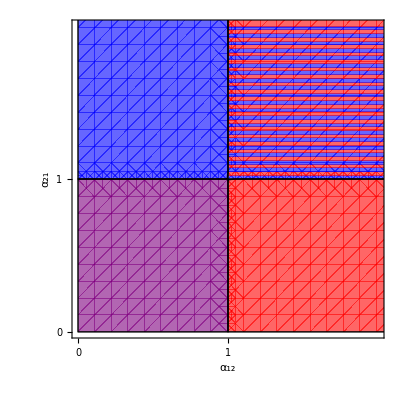

```mathematica
dx=1/41;
coex=RegionPlot[{a12<1&&a21<1},{a12,0,2.1},{a21,0,2.1},PlotStyle->Directive[Purple,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
n1wins=RegionPlot[{a12<1&&a21>1},{a12,0,2.1},{a21,0,2.1},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
n2wins=RegionPlot[{a12>1&&a21<1},{a12,0,2.1},{a21,0,2.1},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
fc=RegionPlot[{a12>1&&a21>1},{a12,0,2.1},{a21,0,2.1},Mesh->{Table[x,{x,0,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
Show[coex,n1wins,n2wins,fc,FrameStyle->Directive[18,Black],FrameLabel->{Style["α_12",21],Style["α_21",21]},
FrameTicks->{{{0,1},None},{{0,1},None}},PlotRangePadding->0,PlotRange->{{0,2},{0,2}}]
```

#### Fig 2 – Effect of dispersal (competitive exclusion case)

```mathematica
r1=r2=1;
α12=1.5;α21=0.5;
k1=k2=50;
nr1=nr2=50;
mvals = {0.005,0.05,0.5,5.0};
```

```mathematica
range=10^Range[-3,1,0.025];
```

```mathematica
(* Fig. 2a – bifurcation diagram *)
N11=N12=N21=N22=coex={};
Do[
m1=m2=i;
veqs=SelectValid[NSolveEcoEq[]];
lveqs = Length[veqs];AppendTo[N11,n1/.veqs[[1]]]; AppendTo[N21,n2/.veqs[[1]]];
If[lveqs>1,AppendTo[N12,n1/.veqs[[3]]], AppendTo[N12,NaN]]; If[lveqs>1,AppendTo[N22,n2/.veqs[[3]]], AppendTo[N22,NaN]],
{i,range}]
```

```mathematica
ListLinePlot[{Transpose[{range,N11}],Transpose[{range,N21}],Transpose[{range,N12}],Transpose[{range,N22}]},
PlotStyle->{Blue,Red,{Blue,Dashing[0.1]},{Red,Dashing[0.1]}},
PlotLabels->{Style["N_1",FontSize->15],Style["N_2",FontSize->15]}, 
Frame->True,
ScalingFunctions->{"Log","Log"},
GridLines->{{{mvals[[1]],Black},{mvals[[2]],Black},{mvals[[3]],Black},{mvals[[4]],Black}},None},
LabelStyle -> Medium
]
```

-Graphics-

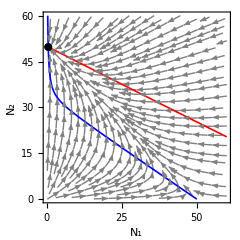

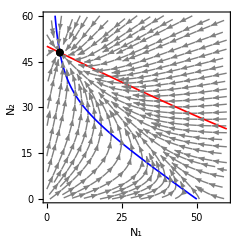

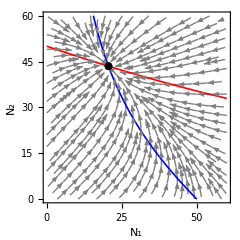

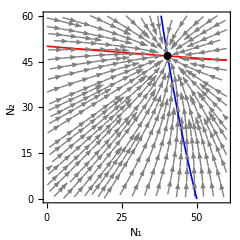

```mathematica
(* Fig. 2b-e — phase planes *)
m1=m2=mvals[[1]];
PlotEcoPhasePlane[{n1,0,60},{n2,0,60},ImageSize->240,BaseStyle->{FontSize->12},FrameLabel->{"N_1","N_2"}]
m1=m2=mvals[[2]];
PlotEcoPhasePlane[{n1,0,60},{n2,0,60},ImageSize->240,BaseStyle->{FontSize->12},FrameLabel->{"N_1","N_2"}]
m1=m2=mvals[[3]];
PlotEcoPhasePlane[{n1,0,60},{n2,0,60},ImageSize->240,BaseStyle->{FontSize->12},FrameLabel->{"N_1","N_2"}]
m1=m2=mvals[[4]];
PlotEcoPhasePlane[{n1,0,60},{n2,0,60},ImageSize->240,BaseStyle->{FontSize->12},FrameLabel->{"N_1","N_2"}]
```

#### Fig 3 – Effect of dispersal (founder control case)

```mathematica
r1=r2=1;
m1=m2=10^-3;
α12=1.4;α21=1.3;
k1=k2=50;
nr1=nr2=50;
mvals = {0.01,0.035,0.05,0.5};
```

```mathematica
mlow=0.35;
mhigh=0.42;
rangelow=10^Range[-3,Log10[mlow],0.025];
rangelow = Drop[rangelow,-1];
rangedense = 10^Range[Log10[mlow],Log10[mhigh],0.0005];
rangehigh = 10^Range[Log10[mhigh],1,0.025];
rangehigh = Drop[rangehigh,1];
range = Join[rangelow,rangedense,rangehigh];
```

```mathematica
N11=N12=N21=N22=coex={};
Do[
m1=m2=i;
veqs=SelectValid[SolveEcoEq[]];lveqs=Length[veqs];AppendTo[N11,n1/.veqs[[1]]]; AppendTo[N21,n2/.veqs[[1]]];
If[lveqs>1,AppendTo[N12,n1/.veqs[[3]]], AppendTo[N12,NaN]]; If[lveqs>1,AppendTo[N22,n2/.veqs[[3]]], AppendTo[N22,NaN]],
{i,range}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
(* Fig. 3a – bifurcation diagram *)ListLinePlot[{Transpose[{range,N11}],Transpose[{range,N21}],Transpose[{range,N12}],Transpose[{range,N22}]},
PlotStyle->{Blue,Red,{Blue,Dashing[0.01]},{Red,Dashing[0.01]}},
PlotLabels->{Style["N_1",FontSize->15],Style["N_2",FontSize->15]}, 
Frame->True,
ScalingFunctions->{"Log","Log"},
GridLines->{{{mvals[[1]],Black},{mvals[[2]],Black},{mvals[[3]],Black},{mvals[[4]],Black}},None},
LabelStyle -> Medium 
]
```

-Graphics-

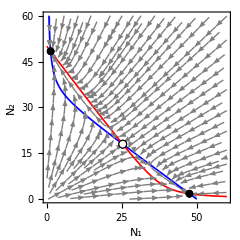

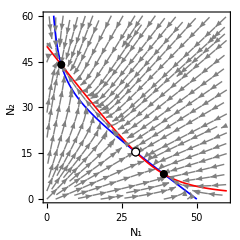

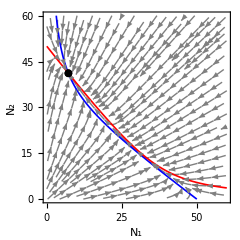

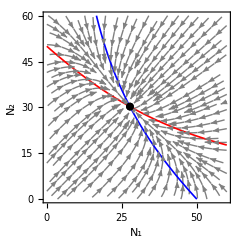

```mathematica
(* Fig. 3b-e — phase planes *)
m1=m2=mvals[[1]];
PlotEcoPhasePlane[{n1,0,60},{n2,0,60},ImageSize->240,BaseStyle->{FontSize->12},FrameLabel->{"N_1","N_2"}]
m1=m2=mvals[[2]];
PlotEcoPhasePlane[{n1,0,60},{n2,0,60},ImageSize->240,BaseStyle->{FontSize->12},FrameLabel->{"N_1","N_2"}]
m1=m2=mvals[[3]];
PlotEcoPhasePlane[{n1,0,60},{n2,0,60},ImageSize->240,BaseStyle->{FontSize->12},FrameLabel->{"N_1","N_2"}]
m1=m2=mvals[[4]];
PlotEcoPhasePlane[{n1,0,60},{n2,0,60},ImageSize->240,BaseStyle->{FontSize->12},FrameLabel->{"N_1","N_2"}]
```

### Fig 4 — Deterministic square pies of basin size

```mathematica
r1=1;r2=1;nr1=50;nr2=50;k1=50;k2=50;
```

```mathematica
(* Fig. 4a — m=10^-1 *)
m1=0.1;m2=0.1;
Clear[α12,α21];
dα=0.1;
Rasterize[Show[Graphics[Flatten[Table[
    Inset[DeterministicSquarePie[DeterministicProbFrac[NSolveEcoEq[]]],{α12,α21},{0,0},dα-0.01]
   ,{α12,0.0,2.0,dα},{α21,0.0,2.0,dα}],1]
  ],Frame->True,PlotRange->{{-0.05-dα/2,2.05+dα/2},{-0.05-dα/2,2.05+dα/2}},FrameTicksStyle->Directive[Black,16],FrameTicks->{{{0,0.5,1,1.5,2},None},{{0,0.5,1,1.5,2},None}},FrameLabel->{Style["α_12",21],Style["α_21",21]}],ImageResolution->300]
```

-Graphics-

```mathematica
(* Fig 4b — m=10^-2 *)
m1=0.01;m2=0.01;
Clear[α12,α21];
dα=0.1;
Rasterize[Show[Graphics[Flatten[Table[
    Inset[DeterministicSquarePie[DeterministicProbFrac[NSolveEcoEq[]]],{α12,α21},{0,0},dα-0.01]
   ,{α12,0.0,2.0,dα},{α21,0.0,2.0,dα}],1]
  ],Frame->True,PlotRange->{{-0.05-dα/2,2.05+dα/2},{-0.05-dα/2,2.05+dα/2}},FrameTicksStyle->Directive[Black,16],FrameTicks->{{{0,0.5,1,1.5,2},None},{{0,0.5,1,1.5,2},None}},FrameLabel->{Style["α_12",21],Style["α_21",21]}],ImageResolution->300]
```

-Graphics-

```mathematica
(* Fig 4c — m=10^-3 *)
m1=0.001;m2=0.001;
Clear[α12,α21];
dα=0.1;
Rasterize[Show[Graphics[Flatten[Table[
    Inset[DeterministicSquarePie[DeterministicProbFrac[NSolveEcoEq[]]],{α12,α21},{0,0},dα-0.01]
   ,{α12,0.0,2.0,dα},{α21,0.0,2.0,dα}],1]
  ],Frame->True,PlotRange->{{-0.05-dα/2,2.05+dα/2},{-0.05-dα/2,2.05+dα/2}},FrameTicksStyle->Directive[Black,16],FrameTicks->{{{0,0.5,1,1.5,2},None},{{0,0.5,1,1.5,2},None}},FrameLabel->{Style["α_12",21],Style["α_21",21]}],ImageResolution->300]
```

-Graphics-

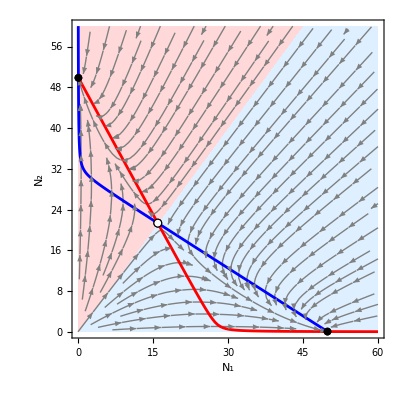

```mathematica
(* Legend *)
α12=1.6;α21=1.8;m1=m2=0.001;
PlotBasins[60]
```

```mathematica
Rasterize@BarLegend[{DeterministicCF,{0,1}},LabelStyle->Directive[Black, 16],Method->{TicksStyle->{Black,Thickness[0.004]},FrameStyle->Directive[Thickness[0.005],Black]},LegendLayout->"Row"]
```

-Graphics-

```mathematica
DeterministicSquarePie[DeterministicProbFrac[NSolveEcoEq[]]]
```

-Graphics-

## Stochastic open system

### Fig 6 — 1 wins (α12=1.25, α21=0.8)

```mathematica
r1=r2=1;
e=0;
k1=k2=50;
{α12,α21}={1.25,0.8};
Setnmax[2k1,2k2];
```

#### a-b) m1=m2=10^-3

```mathematica
{m1,m2}={10^-3,10^-3};
dis=GetDis[{k1,k2}];
WatershedPlot[dis,ImageSize->400]
SquarePie[dis]
```

-Graphics3D-

-Graphics-

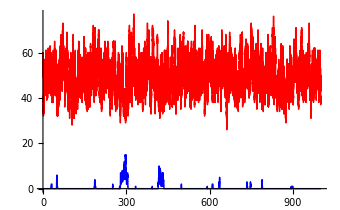

```mathematica
SeedRandom[7];
sol=StochSim[{nr1->k1,nr2->k2},{n1->0,n2->k2},1000];
PlotDynamics[sol,PlotPoints->400,PlotRange->Automatic,AxesLabel->None,ImageSize->340,TicksStyle->frametickstyle,LineStyles->Thickness[0.003]]
```

#### c-d) m1=m2=10^-2

```mathematica
{m1,m2}={10^-2,10^-2};
dis=GetDis[{k1,k2}];
WatershedPlot[dis,ImageSize->400]
SquarePie[dis]
```

-Graphics3D-

-Graphics-

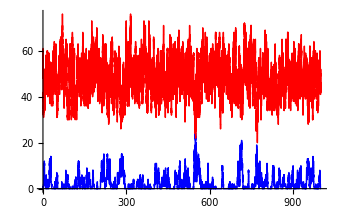

```mathematica
SeedRandom[7];
sol=StochSim[{nr1->k1,nr2->k2},{n1->0,n2->k2},1000];
PlotDynamics[sol,PlotPoints->400,PlotRange->Automatic,AxesLabel->None,ImageSize->340,TicksStyle->frametickstyle,LineStyles->Thickness[0.003]]
```

#### e-f) m1=m2=10^-1

```mathematica
{m1,m2}={10^-1,10^-1};
dis=GetDis[{k1,k2}];
WatershedPlot[dis,ImageSize->400]
SquarePie[dis]
```

-Graphics3D-

-Graphics-

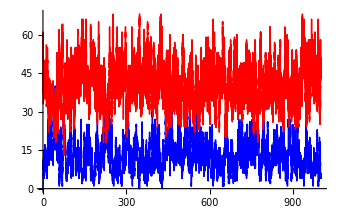

```mathematica
SeedRandom[7];
sol=StochSim[{nr1->k1,nr2->k2},{n1->0,n2->k2},1000];
PlotDynamics[sol,PlotPoints->400,PlotRange->Automatic,AxesLabel->None,ImageSize->340,TicksStyle->frametickstyle,LineStyles->Thickness[0.003]]
```

### Fig 7 — coexistence (α12=α21=0.9)

```mathematica
r1=r2=1;
e=0;
k1=50;k2=50;
{α12,α21}={0.9,0.9};
Setnmax[2k1,2k2];
```

#### a-b) m1=m2=10^-3

```mathematica
{m1,m2}={10^-3,10^-3};
dis=GetDis[{k1,k2}];
WatershedPlot[dis,ImageSize->400]
SquarePie[dis]
```

-Graphics3D-

-Graphics-

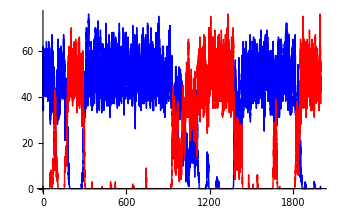

```mathematica
SeedRandom[7];
sol=StochSim[{nr1->k1,nr2->k2},eq[[2]],2000];
PlotDynamics[sol,PlotPoints->400,PlotRange->Automatic,AxesLabel->None,ImageSize->340,TicksStyle->frametickstyle,LineStyles->Thickness[0.003]]
```

#### c-d) m1=m2=10^-2

```mathematica
{m1,m2}={10^-2,10^-2};
dis=GetDis[{k1,k2}];
WatershedPlot[dis,ImageSize->400]
SquarePie[dis]
```

-Graphics3D-

-Graphics-

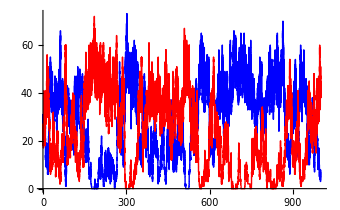

```mathematica
SeedRandom[7];
sol=StochSim[{nr1->k1,nr2->k2},eq[[-1]],1000];
PlotDynamics[sol,PlotPoints->400,PlotRange->Automatic,AxesLabel->None,ImageSize->340,TicksStyle->frametickstyle,LineStyles->Thickness[0.003]]
```

#### e-f) m1=m2=10^-1

```mathematica
{m1,m2}={10^-1,10^-1};
dis=GetDis[{k1,k2}];
WatershedPlot[dis,ImageSize->400]
SquarePie[dis]
```

-Graphics3D-

-Graphics-

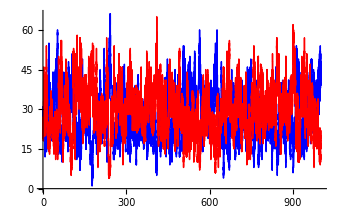

```mathematica
SeedRandom[7];
sol=StochSim[{nr1->k1,nr2->k2},eq[[-1]],1000];
PlotDynamics[sol,PlotPoints->400,PlotRange->Automatic,AxesLabel->None,ImageSize->340,TicksStyle->frametickstyle,LineStyles->Thickness[0.003]]
```

### Fig 8 — founder control (α12=1.2, α21=1.2)

```mathematica
r1=r2=1;
e=0;
k1=50;k2=50;
{α12,α21}={1.2,1.2};
Setnmax[2k1,2k2];
```

#### a-b) m1=m2=10^-3

```mathematica
{m1,m2}={10^-3,10^-3};
dis=GetDis[{k1,k2}];
WatershedPlot[dis,ImageSize->400]
SquarePie[dis]
```

-Graphics3D-

-Graphics-

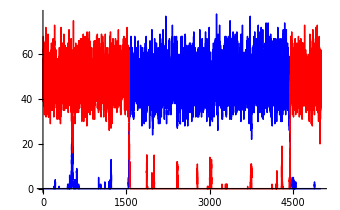

```mathematica
SeedRandom[3];
sol=StochSim[{nr1->k1,nr2->k2},{n1->0,n2->k2},5000];
PlotDynamics[sol,PlotPoints->400,PlotRange->Automatic,AxesLabel->None,ImageSize->340,TicksStyle->frametickstyle,LineStyles->Thickness[0.003]]
```

#### c-d) m1=m2=10^-1.5

```mathematica
{m1,m2}={10^-1.5,10^-1.5};
dis=GetDis[{k1,k2}];
WatershedPlot[dis,ImageSize->400]
SquarePie[dis]
```

-Graphics3D-

-Graphics-

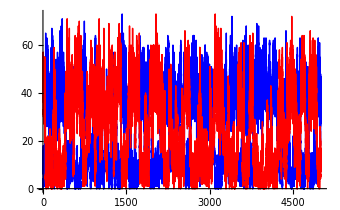

```mathematica
SeedRandom[3];
sol=StochSim[{nr1->k1,nr2->k2},{n1->0,n2->k2},5000];
PlotDynamics[sol,PlotPoints->400,PlotRange->Automatic,AxesLabel->None,ImageSize->340,TicksStyle->frametickstyle,LineStyles->Thickness[0.003]]
```

#### e-f) m1=m2=10^-1

```mathematica
{m1,m2}={10^-1,10^-1};
dis=GetDis[{k1,k2}];
WatershedPlot[dis,ImageSize->400]
SquarePie[dis]
```

-Graphics3D-

-Graphics-

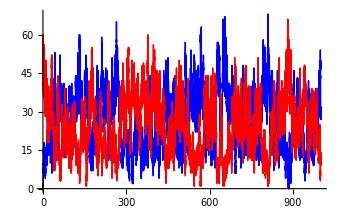

```mathematica
SeedRandom[3];
sol=StochSim[{nr1->k1,nr2->k2},{n1->0,n2->k2},1000];
PlotDynamics[sol,PlotPoints->400,PlotRange->Automatic,AxesLabel->None,ImageSize->340,TicksStyle->frametickstyle,LineStyles->Thickness[0.003]]
```

### Fig 9 — α scan, various m

```mathematica
r1=r2=1;
e=0;
k1=50;k2=50;
Setnmax[2k1,2k2];
dα=0.1;
```

```mathematica
(* Fig 9a *)
m1=m2=10^-1;
Rasterize[Show[Graphics[Flatten[Monitor[Table[
    Inset[SquarePie[GetDis[{k1,k2}]],{α12,α21},{0,0},dα-0.01]
   ,{α12,0.0,2.0,dα},{α21,0.0,2.0,dα}],{α12,α21}],1]
  ],Frame->True,PlotRange->{{-0.05-dα/2,2.05+dα/2},{-0.05-dα/2,2.05+dα/2}},FrameTicksStyle->frametickstyle,FrameTicks->{{{0,0.5,1,1.5,2},None},{{0,0.5,1,1.5,2},None}},FrameLabel->{Style["α_12",21],Style["α_21",21]}],ImageResolution->300]
```

-Graphics-

```mathematica
(* Fig 9b *)
m1=m2=10^-2;
Rasterize[Show[Graphics[Flatten[Monitor[Table[
    Inset[SquarePie[GetDis[{k1,k2}]],{α12,α21},{0,0},dα-0.01]
   ,{α12,0.0,2.0,dα},{α21,0.0,2.0,dα}],{α12,α21}],1]
  ],Frame->True,PlotRange->{{-0.05-dα/2,2.05+dα/2},{-0.05-dα/2,2.05+dα/2}},FrameTicksStyle->frametickstyle,FrameTicks->{{{0,0.5,1,1.5,2},None},{{0,0.5,1,1.5,2},None}},FrameLabel->{Style["α_12",21],Style["α_21",21]}],ImageResolution->300]
```

-Graphics-

```mathematica
(* Fig 9c *)
m1=m2=10^-3;
Rasterize[Show[Graphics[Flatten[Monitor[Table[
    Inset[SquarePie[GetDis[{k1,k2}]],{α12,α21},{0,0},dα-0.01]
   ,{α12,0.0,2.0,dα},{α21,0.0,2.0,dα}],{α12,α21}],1]
  ],Frame->True,PlotRange->{{-0.05-dα/2,2.05+dα/2},{-0.05-dα/2,2.05+dα/2}},FrameTicksStyle->frametickstyle,FrameTicks->{{{0,0.5,1,1.5,2},None},{{0,0.5,1,1.5,2},None}},FrameLabel->{Style["α_12",21],Style["α_21",21]}],ImageResolution->300]
```

-Graphics-

```mathematica
(* legend *)
BarLegend[{cf,{0.001,0.999}},LabelStyle->Directive[Black, 16],Method->{TicksStyle->{Black,Thickness[0.004]},FrameStyle->Directive[Thickness[0.005],Black]},LegendLayout->"Row"]
Graphics[{EdgeForm[Thickness[0.08]],Red,Rectangle[]},ImageSize->20]
Graphics[{EdgeForm[Thickness[0.08]],Blue,Rectangle[]},ImageSize->20]
```

-Graphics-

-Graphics-

### Appendix S3: Fig S1 — α scan, various K

```mathematica
r1=r2=1;
e=0;
m1=m2=10^-3;
dα=0.1;
```

```mathematica
(* Appendix S3: Fig. S1a *)
k1=50;k2=50;
Setnmax[2k1,2k2];

Rasterize[Show[Graphics[Flatten[Monitor[Table[
    Inset[SquarePie[GetDis[{k1,k2}]],{α12,α21},{0,0},dα-0.01]
   ,{α12,0.0,2.0,dα},{α21,0.0,2.0,dα}],{α12,α21}],1]
  ],Frame->True,PlotRange->{{-0.05-dα/2,2.05+dα/2},{-0.05-dα/2,2.05+dα/2}},FrameTicksStyle->frametickstyle,FrameTicks->{{{0,0.5,1,1.5,2},None},{{0,0.5,1,1.5,2},None}},FrameLabel->{Style["α_12",21],Style["α_21",21]}],ImageResolution->300]
```

-Graphics-

```mathematica
(* Appendix S3: Fig. S1b *)
k1=100;k2=100;
Setnmax[2k1,2k2];

Rasterize[Show[Graphics[Flatten[Monitor[Table[
    Inset[SquarePie[GetDis[{k1,k2}]],{α12,α21},{0,0},dα-0.01]
   ,{α12,0.0,2.0,dα},{α21,0.0,2.0,dα}],{α12,α21}],1]
  ],Frame->True,PlotRange->{{-0.05-dα/2,2.05+dα/2},{-0.05-dα/2,2.05+dα/2}},FrameTicksStyle->frametickstyle,FrameTicks->{{{0,0.5,1,1.5,2},None},{{0,0.5,1,1.5,2},None}},FrameLabel->{Style["α_12",21],Style["α_21",21]}],ImageResolution->300]
```

-Graphics-

```mathematica
(* Appendix S3: Fig. S1c *)
k1=200;k2=200;
Setnmax[2k1,2k2];

Rasterize[Show[Graphics[Flatten[Monitor[Table[
    Inset[SquarePie[GetDis[{k1,k2}]],{α12,α21},{0,0},dα-0.01]
   ,{α12,0.0,2.0,dα},{α21,0.0,2.0,dα}],{α12,α21}],1]
  ],Frame->True,PlotRange->{{-0.05-dα/2,2.05+dα/2},{-0.05-dα/2,2.05+dα/2}},FrameTicksStyle->frametickstyle,FrameTicks->{{{0,0.5,1,1.5,2},None},{{0,0.5,1,1.5,2},None}},FrameLabel->{Style["α_12",21],Style["α_21",21]}],ImageResolution->300]
```

-Graphics-

### Appendix S2: Fig S1 — first passage time exploration

```mathematica
r1=r2=1;
e=0;
m1=m2=10^-3;
α12=1.2;α21=1.3;
```

#### Appendix S2: Fig S1A

```mathematica
P1={};
P2={};
P12={};
P21={};
```

```mathematica
range=Range[25,200,1];
```

```mathematica
Do[k1=k2=i;
Setnmax[2 k1,2  k2];dis=GetDis[{k1,k2}];
pf=ProbFrac[dis];If[MemberQ[Keys[pf],0.],AppendTo[P1,0./.pf],AppendTo[P1,0.] ];
If[MemberQ[Keys[pf],1.],AppendTo[P2,1./.pf] ,AppendTo[P2,0.]];AppendTo[P12,Max[DeleteCases[Keys[pf],a_/;MemberQ[{-1,0.,1.},a]]]/.pf]; 
AppendTo[P21,Min[DeleteCases[Keys[pf],a_/;MemberQ[{-1,0.,1.},a]]]/.pf];, 
{i,range}]
```

```mathematica
Rasterize[ListLinePlot[{Transpose[{range,P2}],Transpose[{range,P1}],Transpose[{range,P12}],Transpose[{range,P21}]},PlotStyle->{Red,Blue,{Green,Dashed},{Orange,Dashed}},PlotLabels->{Style["P_2",FontSize->15],Style["P_1",FontSize->15]}, Frame->True,PlotRange->{{25,200},{0,1}},GridLines->{{{40,Directive[Black,Thick]},{150,Directive[Black,Thick]}},{{0.372228883266225,Directive[Red,Dashed,Thick]},{0.6277711167337751,Directive[Blue,Dashed,Thick]}}},FrameTicksStyle->Medium, AspectRatio->1],ImageResolution->500]
```

-Graphics-

#### Appendix S2: Fig S1B

```mathematica
TMNorm[k1_,k2_]:=Module[{DiagNorm, DiagNormMatrix, TMZeroDiag},
DiagNorm=-Total[TM[k1,k2]-DiagonalMatrix[Diagonal@TM[k1,k2]]];
DiagNormMatrix=SparseArray[Band[{1,1}]->DiagNorm,Dimensions[TM[k1,k2]]] ;
TMZeroDiag=SparseArray[TM[k1,k2]-DiagonalMatrix[Diagonal[TM[k1,k2]]]];
Return[TMZeroDiag+DiagNormMatrix];
]
```

```mathematica
GetDisNorm[{nr1_,nr2_}]:=Module[{vec},
vec=Eigenvectors[TMNorm[nr1,nr2],-1,Method->"Arnoldi"]⟦1⟧;
vec/=Total[vec]
];
```

```mathematica
(* calculates mean first-passage time *)
MFPT[{nr1_,nr2_},{n1i_,n2i_}->{n1f_,n2f_}]:=LinearSolve[DeleteRowAndColumn[Transpose[TMNorm[k1,k2]],(n1f+1)+n2f*(n1max+1)],ConstantArray[-1,Dimensions[TM[k1,k2]-1][[1]]-1]][[n1i+1+n2i*(n1max+1)]]
```

```mathematica
k2tok1norm=Table[k1=k2=i;
Setnmax[2k1,2k2];MFPT[{k1,k2},{0,k2}->{k1,0}],{i,25,200,2}];
```

```mathematica
k1tok2norm=Table[k1=k2=i;
Setnmax[2k1,2k2];MFPT[{k1,k2},{k1,0}->{0,k2}],{i,25,200,2}];
```

```mathematica
Rasterize[ListLinePlot[{Transpose[{Range[25,200,2],k2tok1norm}],Transpose[{Range[25,200,2],k1tok2norm}]},PlotStyle->{Red,Blue}, Frame->True,PlotRange->{{25,200},All},GridLines->{{{40,Directive[Black,Thick]},{150,Directive[Black,Thick]}},{}},LabelStyle->Medium, AspectRatio->1,ScalingFunctions->{"Linear","Log10"},PlotLabels->{Style["T_K_2",15],Style["T_K_1",15]}],ImageResolution->500]
```

-Graphics-

#### Appendix S2: Fig S1C-D

```mathematica
(* Appendix S2: Fig S1C *)
nr1=nr2=k1=k2=40;
Setnmax[2k1,2k2]
dis=GetDis[{k1,k2}];
Rasterize[PlotDis[dis],ImageResolution->500]
```

-Graphics-

```mathematica
(* Appendix S2: Fig S1D *)
nr1=nr2=k1=k2=150;
Setnmax[2k1,2k2]
dis=GetDis[{k1,k2}];
Rasterize[PlotDis[dis],ImageResolution->500]
```

-Graphics-

## Metacommunity model

### Fig 10 — α12-α21, equal m

```mathematica
Clear[nr1,nr2,α12,α21];
r1=r2=1;
k1=k2=50;
e=0;
Setnmax[2k1,2k2]
```

```mathematica
(* invasion rates *)
λ12[α12in_?NumericQ,α21in_?NumericQ]:=λ12[α12in,α21in]=Block[{α12=α12in,α21=α21in},Inv1[nr2/.Eq2]];
λ21[α12in_?NumericQ,α21in_?NumericQ]:=λ21[α12in,α21in]=Block[{α12=α12in,α21=α21in},Inv2[nr1/.Eq1]];
```

```mathematica
dx=1/41; (* grid spacing for stripes *)
```

Note: these take a few minutes each.

#### a) m=10^0

```mathematica
m1=m2=10^0;
```

```mathematica
ClearCache[λ12,λ21]
```

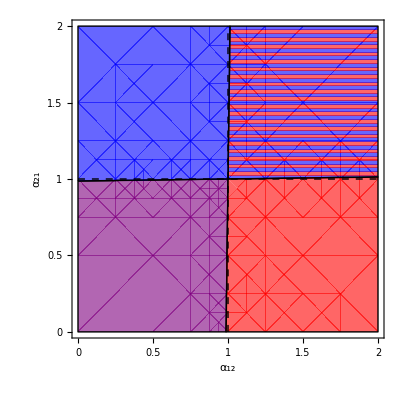

```mathematica
fc=RegionPlot[λ12[α12in,α21in]<1&&λ21[α12in,α21in]<1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,Mesh->{Table[x,{x,0,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
inv1=RegionPlot[λ12[α12in,α21in]>1&&λ21[α12in,α21in]<1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
inv2=RegionPlot[λ12[α12in,α21in]<1&&λ21[α12in,α21in]>1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
coex=RegionPlot[λ12[α12in,α21in]>1&&λ21[α12in,α21in]>1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Purple,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
Show[coex,fc,inv1,inv2,
Graphics[{{Dashed,Black,Line[{{1,0},{1,2}}]},{Dashed,Black,Line[{{0,1},{2,1}}]}}],FrameStyle->Directive[18,Black],FrameLabel->{Style["α_12",21],Style["α_21",21]},
FrameTicks->{{{0,0.5,1,1.5,2},None},{{0,0.5,1,1.5,2},None}},PlotRangePadding->0]
```

#### b) m=10^-1

```mathematica
m1=m2=10^-1;
```

```mathematica
ClearCache[λ12,λ21]
```

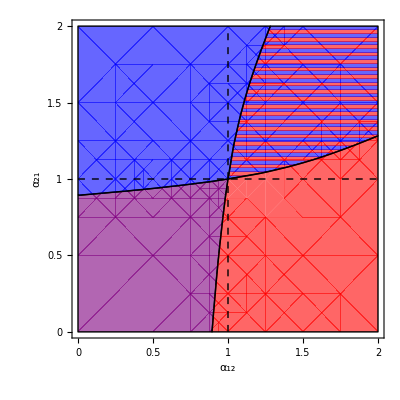

```mathematica
fc=RegionPlot[λ12[α12in,α21in]<1&&λ21[α12in,α21in]<1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,Mesh->{Table[x,{x,0,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
inv1=RegionPlot[λ12[α12in,α21in]>1&&λ21[α12in,α21in]<1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
inv2=RegionPlot[λ12[α12in,α21in]<1&&λ21[α12in,α21in]>1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
coex=RegionPlot[λ12[α12in,α21in]>1&&λ21[α12in,α21in]>1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Purple,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
Show[coex,fc,inv1,inv2,
Graphics[{{Dashed,Black,Line[{{1,0},{1,2}}]},{Dashed,Black,Line[{{0,1},{2,1}}]}}],FrameStyle->Directive[18,Black],FrameLabel->{Style["α_12",21],Style["α_21",21]},
FrameTicks->{{{0,0.5,1,1.5,2},None},{{0,0.5,1,1.5,2},None}},PlotRangePadding->0]
```

#### c) m=10^-2

```mathematica
m1=m2=10^-2;
```

```mathematica
ClearCache[λ12,λ21]
```

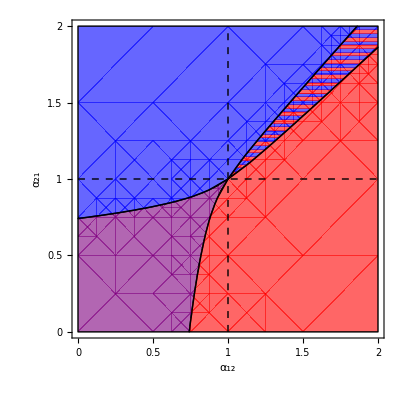

```mathematica
(* 145s *)
fc=RegionPlot[λ12[α12in,α21in]<1&&λ21[α12in,α21in]<1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,Mesh->{Table[x,{x,0,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
inv1=RegionPlot[λ12[α12in,α21in]>1&&λ21[α12in,α21in]<1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
inv2=RegionPlot[λ12[α12in,α21in]<1&&λ21[α12in,α21in]>1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
coex=RegionPlot[λ12[α12in,α21in]>1&&λ21[α12in,α21in]>1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Purple,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
Show[coex,fc,inv1,inv2,
Graphics[{{Dashed,Black,Line[{{1,0},{1,2}}]},{Dashed,Black,Line[{{0,1},{2,1}}]}}],FrameStyle->Directive[18,Black],FrameLabel->{Style["α_12",21],Style["α_21",21]},
FrameTicks->{{{0,0.5,1,1.5,2},None},{{0,0.5,1,1.5,2},None}},PlotRangePadding->0]
```

#### d) m=10^-3

```mathematica
m1=m2=10^-3;
```

```mathematica
ClearCache[λ12,λ21]
```

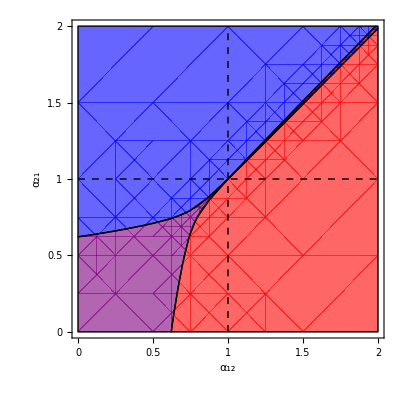

```mathematica
fc=RegionPlot[λ12[α12in,α21in]<1&&λ21[α12in,α21in]<1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,Mesh->{Table[x,{x,0,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
inv1=RegionPlot[λ12[α12in,α21in]>1&&λ21[α12in,α21in]<1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
inv2=RegionPlot[λ12[α12in,α21in]<1&&λ21[α12in,α21in]>1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
coex=RegionPlot[λ12[α12in,α21in]>1&&λ21[α12in,α21in]>1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Purple,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
Show[coex,fc,inv1,inv2,
Graphics[{{Dashed,Black,Line[{{1,0},{1,2}}]},{Dashed,Black,Line[{{0,1},{2,1}}]}}],FrameStyle->Directive[18,Black],FrameLabel->{Style["α_12",21],Style["α_21",21]},
FrameTicks->{{{0,0.5,1,1.5,2},None},{{0,0.5,1,1.5,2},None}},PlotRangePadding->0]
```

### Appendix S3: Fig S2 — squarepies in coex region

```mathematica
Clear[nr1,nr2,α12,α21];
r1=r2=1;
k1=k2=50;
e=0;
Setnmax[2k1,2k2];
```

```mathematica
(* invasion rates *)λ12[α12in_?NumericQ,α21in_?NumericQ]:=λ12[α12in,α21in]=Block[{α12=α12in,α21=α21in},Inv1[nr2/.Eq2]];
λ21[α12in_?NumericQ,α21in_?NumericQ]:=λ21[α12in,α21in]=Block[{α12=α12in,α21=α21in},Inv2[nr1/.Eq1]];
```

```mathematica
m1=m2=10^-2;
```

```mathematica
ClearCache[λ12,λ21]
```

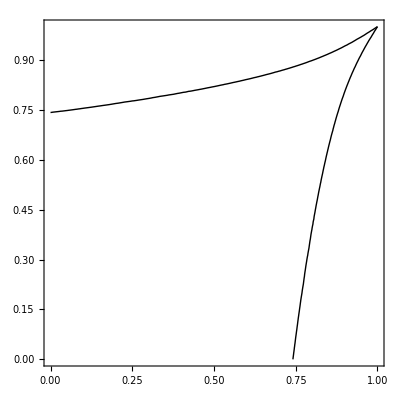

```mathematica
coexplot=ContourPlot[{λ12[α12in,α21in]==1,λ21[α12in,α21in]==1},{α12in,0,1},{α21in,0,1},PlotPoints->5,MaxRecursion->3,ContourStyle->Directive[Thick,Black],Background->Opacity[0]]
```

Note: these take 30-60 minutes.

```mathematica
Clear[α12,α21];
dα=0.02;
pies=Graphics[Flatten[Table[
    Inset[SquarePie[GetDis[{nr1,nr2}/.Eq12]],{α12,α21},{0,0},dα]
   ,{α12,0.0,1.0,dα},{α21,0.0,1.0,dα}],1]
  ];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
Rasterize[Show[pies,coexplot,Frame->True,PlotRange->{{-0.02-dα/2,1.02+dα/2},{-0.02-dα/2,1.02+dα/2}},FrameTicksStyle->frametickstyle,FrameTicks->Automatic,FrameLabel->{Style["α_12",21],Style["α_21",21]}],ImageResolution->300]
```

-Graphics-

```mathematica
m1=m2=10^-5;
```

```mathematica
ClearCache[λ12,λ21]
```

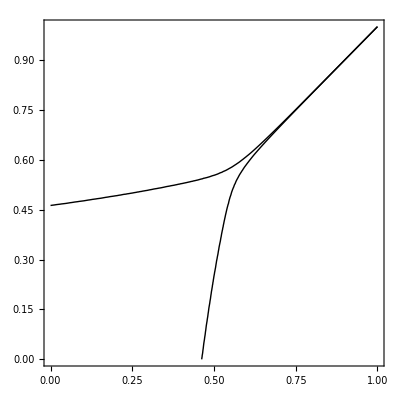

```mathematica
coexplot=ContourPlot[{λ12[α12in,α21in]==1,λ21[α12in,α21in]==1},{α12in,0,1},{α21in,0,1},PlotPoints->5,MaxRecursion->3,ContourStyle->Directive[Thick,Black],Background->Opacity[0]]
```

```mathematica
Clear[α12,α21];
dα=0.02;
pies=Graphics[Flatten[Table[
    Inset[SquarePie[GetDis[{nr1,nr2}/.Eq12]],{α12,α21},{0,0},0.99dα]
   ,{α12,0.0,1.0,dα},{α21,0.0,1.0,dα}],1]
  ];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
Rasterize[Show[pies,coexplot,Frame->True,PlotRange->{{-0.02-dα/2,1.02+dα/2},{-0.02-dα/2,1.02+dα/2}},FrameTicksStyle->frametickstyle,FrameTicks->Automatic,FrameLabel->{Style["α_12",21],Style["α_21",21]}],ImageResolution->300]
```

-Graphics-

### Appendix S3: Fig S3 — effect of K on outcome

```mathematica
Clear[nr1,nr2,α12,α21];
r1=r2=1;
m1=m2=0.01;
e=0;
```

```mathematica
(* invasion rates *)
λ12[α12in_?NumericQ,α21in_?NumericQ]:=λ12[α12in,α21in]=Block[{α12=α12in,α21=α21in},Inv1[nr2/.Eq2]];
λ21[α12in_?NumericQ,α21in_?NumericQ]:=λ21[α12in,α21in]=Block[{α12=α12in,α21=α21in},Inv2[nr1/.Eq1]];
```

```mathematica
k1=k2=50;
Setnmax[2k1,2k2]
ClearCache[λ12,λ21]
```

```mathematica
out501=ContourPlot[λ12[α12in,α21in]==1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,ContourStyle->{Gray,Dotted},FrameLabel->{"α12","α21"}];
out502=MapAt[GeometricTransformation[#,ReflectionMatrix[{-1,1}]]&,out501,{1}];
Show[out501,out502]
```

-Graphics-

```mathematica
k1=k2=100;
Setnmax[2k1,2k2]
ClearCache[λ12,λ21]
```

```mathematica
out1001=ContourPlot[λ12[α12in,α21in]==1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,ContourStyle->{Gray,Dashed},FrameLabel->{"α12","α21"}];
out1002=MapAt[GeometricTransformation[#,ReflectionMatrix[{-1,1}]]&,out1001,{1}];
Show[out1001,out1002]
```

-Graphics-

```mathematica
k1=k2=200;
Setnmax[2k1,2k2]
ClearCache[λ12,λ21]
```

```mathematica
(* ~ 1hr! *)out2001=ContourPlot[λ12[α12in,α21in]==1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->4,ContourStyle->Gray,FrameLabel->{"α12","α21"}];
out2002=MapAt[GeometricTransformation[#,ReflectionMatrix[{-1,1}]]&,out2001,{1}];
Show[out2001,out2002]
```

-Graphics-

```mathematica
Show[out501,out502,out1001,out1002,out2001,out2002]
```

-Graphics-

### Fig 11 — m1-m2, equal α, e=0

```mathematica
r1=r2=1;
k1=k2=50;
e=0;
Setnmax[2k1,2k2]
```

```mathematica
Clear[m1,m2]
```

```mathematica
(* invasion rates *)
λ12[m1in_?NumericQ,m2in_?NumericQ]:=λ12[m1in,m2in]=({m1,m2}={m1in,m2in};Inv1[nr2/.Eq2]);
λ21[m1in_?NumericQ,m2in_?NumericQ]:=λ21[m1in,m2in]=({m1,m2}={m1in,m2in};Inv2[nr1/.Eq1]);
```

```mathematica
dx=3/41; (* spacing for stripes *)
```

Note: these take a few minutes each.

#### a) α12=α21=0.9

```mathematica
α12=α21=0.9;
```

```mathematica
ClearCache[λ12,λ21];
Clear[m1,m2]
```

```mathematica
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
coex=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Purple,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

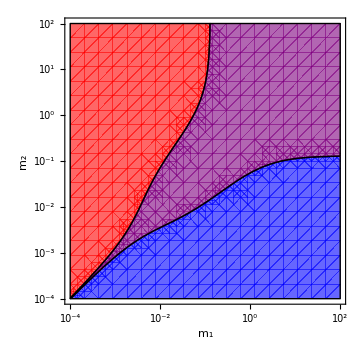

```mathematica
Show[n1wins,n2wins,coex,FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},BoundaryStyle->Directive[Black,Thick],ImageSize->Medium,PlotRange->{{-4,2},{-4,2}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-4,2}],None},{Table[{x,Superscript["10",x]},{x,-4,2}],None}}]
```

#### b) α12=α21=0.99

```mathematica
α12=α21=0.99;
```

```mathematica
ClearCache[λ12,λ21];
Clear[m1,m2]
```

```mathematica
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
coex=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Purple,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

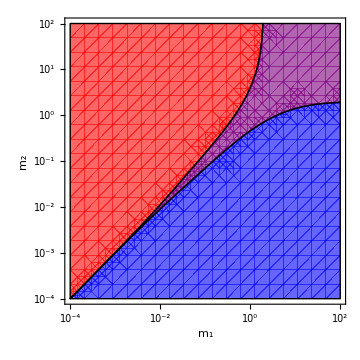

```mathematica
Show[n1wins,n2wins,coex,FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},BoundaryStyle->Directive[Black,Thick],ImageSize->Medium,PlotRange->{{-4,2},{-4,2}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-4,2}],None},{Table[{x,Superscript["10",x]},{x,-4,2}],None}}]
```

#### c) α12=α21=1

```mathematica
α12=α21=1;
```

```mathematica
ClearCache[λ12,λ21];
Clear[m1,m2]
```

```mathematica
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

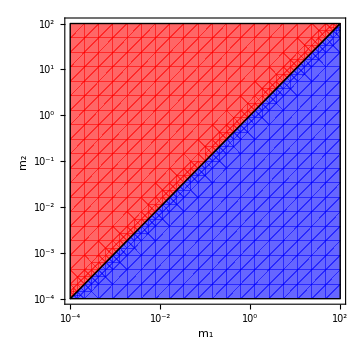

```mathematica
Show[n1wins,n2wins,FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},BoundaryStyle->Directive[Black,Thick],ImageSize->Medium,PlotRange->{{-4,2},{-4,2}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-4,2}],None},{Table[{x,Superscript["10",x]},{x,-4,2}],None}}]
```

#### d) α12=α21=1.01

```mathematica
α12=α21=1.01;
```

```mathematica
ClearCache[λ12,λ21];
Clear[m1,m2]
```

```mathematica
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
fc=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]<1,{m1p,-4,2},{m2p,-4,2},Mesh->{Table[x,{x,-4,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
```

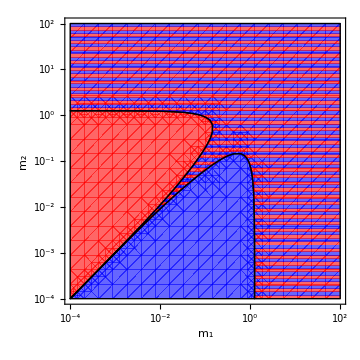

```mathematica
Show[n1wins,n2wins,fc,FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},BoundaryStyle->Directive[Black,Thick],ImageSize->Medium,PlotRange->{{-4,2},{-4,2}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-4,2}],None},{Table[{x,Superscript["10",x]},{x,-4,2}],None}}]
```

#### e) α12=α21=1.1

```mathematica
α12=α21=1.1;
```

```mathematica
ClearCache[λ12,λ21];
Clear[m1,m2]
```

```mathematica
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
fc=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]<1,{m1p,-4,2},{m2p,-4,2},Mesh->{Table[x,{x,-4,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
```

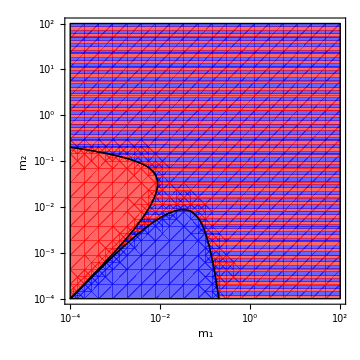

```mathematica
Show[n1wins,n2wins,fc,FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},BoundaryStyle->Directive[Black,Thick],ImageSize->Medium,PlotRange->{{-4,2},{-4,2}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-4,2}],None},{Table[{x,Superscript["10",x]},{x,-4,2}],None}}]
```

#### f) α12=α21=1.5

```mathematica
α12=α21=1.5;
```

```mathematica
ClearCache[λ12,λ21];
Clear[m1,m2]
```

```mathematica
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
fc=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]<1,{m1p,-4,2},{m2p,-4,2},Mesh->{Table[x,{x,-4,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
```

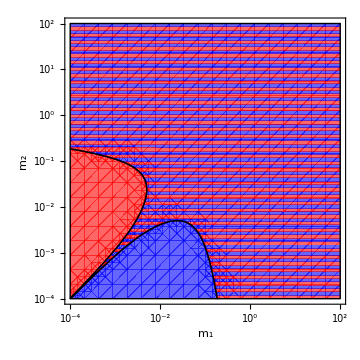

```mathematica
Show[n1wins,n2wins,fc,FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},BoundaryStyle->Directive[Black,Thick],ImageSize->Medium,PlotRange->{{-4,2},{-4,2}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-4,2}],None},{Table[{x,Superscript["10",x]},{x,-4,2}],None}}]
```

### Appendix S3: Fig S4 — m1-m2, equal α, e=0.01

```mathematica
r1=r2=1;
k1=k2=50;
e=0.01;
Setnmax[2k1,2k2]
```

```mathematica
Clear[m1,m2]
```

```mathematica
ClearCache[λ10,λ20]
```

```mathematica
λ10[m1in_?NumericQ]:=(m1=m1in;NrInOut1[ϵ]/ϵ);
λ20[m2in_?NumericQ]:=(m2=m2in;NrInOut2[ϵ]/ϵ);
```

```mathematica
λ10[10^-3]
```

4.57838

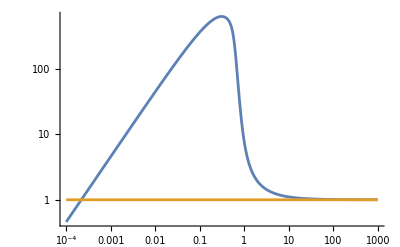

-Graphics-

```mathematica
Clear[m1,m2];
LogLogPlot[{λ10[m1i],1},{m1i,10^-4,10^3},PlotRange->All]
LogLogPlot[{λ20[m2i],1},{m2i,10^-4,10^3},PlotRange->All]
```

```mathematica
(* what is the minimum m1 where species 1 can persist by itself? *)
FindRoot[λ10[10^m1p]==1,{m1p,-3}]
```

{m1p→-3.66143}

```mathematica
(* invasion rate *)
λ12[m1in_?NumericQ,m2in_?NumericQ]:=λ12[m1in,m2in]=({m1,m2}={m1in,m2in};Inv1[nr2/.Eq2]);
λ21[m1in_?NumericQ,m2in_?NumericQ]:=λ21[m1in,m2in]=({m1,m2}={m1in,m2in};Inv2[nr1/.Eq1]);
```

```mathematica
dx=3/41; (* spacing for stripes *)
```

Note: these take a few minutes each.

#### a) α12=α21=0.9

```mathematica
α12=α21=0.9;
```

```mathematica
ClearCache[λ12,λ21];
Clear[m1,m2]
```

```mathematica
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-3.6614287292541534,2},{m2p,-4,2},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-3.6614287292541534,2},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
coex=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]>1,{m1p,-3.6614287292541534,2},{m2p,-3.6614287292541534,2},PlotStyle->Directive[Purple,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

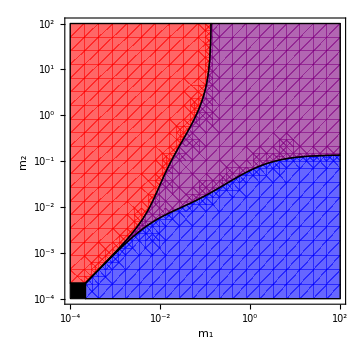

```mathematica
Show[n1wins,n2wins,coex,Graphics[{Black,EdgeForm[Thick],Rectangle[{-4,-4},{-3.66,-3.66}]}],FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},BoundaryStyle->Directive[Black,Thick],ImageSize->Medium,PlotRange->{{-4,2},{-4,2}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-4,2}],None},{Table[{x,Superscript["10",x]},{x,-4,2}],None}}]
```

#### b) α12=α21=0.99

```mathematica
α12=α21=0.99;
```

```mathematica
ClearCache[λ12,λ21];
Clear[m1,m2]
```

```mathematica
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-3.6614287292541534,2},{m2p,-4,2},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-3.6614287292541534,2},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
coex=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]>1,{m1p,-3.6614287292541534,2},{m2p,-3.6614287292541534,2},PlotStyle->Directive[Purple,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

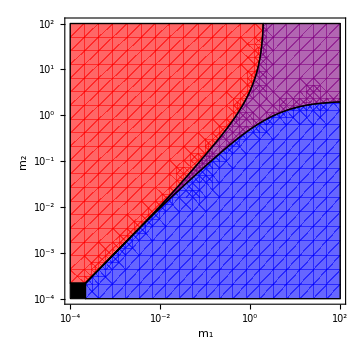

```mathematica
Show[n1wins,n2wins,coex,Graphics[{Black,EdgeForm[Thick],Rectangle[{-4,-4},{-3.66,-3.66}]}],FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},BoundaryStyle->Directive[Black,Thick],ImageSize->Medium,PlotRange->{{-4,2},{-4,2}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-4,2}],None},{Table[{x,Superscript["10",x]},{x,-4,2}],None}}]
```

#### c) α12=α21=1

```mathematica
α12=α21=1;
```

```mathematica
ClearCache[λ12,λ21];
Clear[m1,m2]
```

```mathematica
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-3.6614287292541534,2},{m2p,-4,2},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-3.6614287292541534,2},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

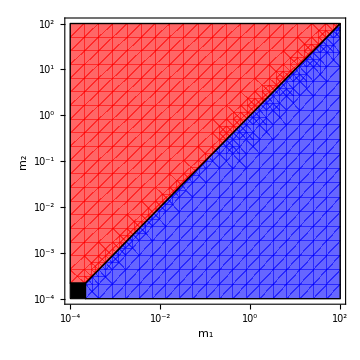

```mathematica
Show[n1wins,n2wins,Graphics[{Black,EdgeForm[Thick],Rectangle[{-4,-4},{-3.66,-3.66}]}],FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},BoundaryStyle->Directive[Black,Thick],ImageSize->Medium,PlotRange->{{-4,2},{-4,2}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-4,2}],None},{Table[{x,Superscript["10",x]},{x,-4,2}],None}}]
```

#### d) α12=α21=1.01

```mathematica
α12=α21=1.01;
```

```mathematica
ClearCache[λ12,λ21];
Clear[m1,m2]
```

```mathematica
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-3.6614287292541534,2},{m2p,-4,2},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-3.6614287292541534,2},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
fc=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]<1,{m1p,-3.6614287292541534,2},{m2p,-3.6614287292541534,2},Mesh->{Table[x,{x,-4,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
```

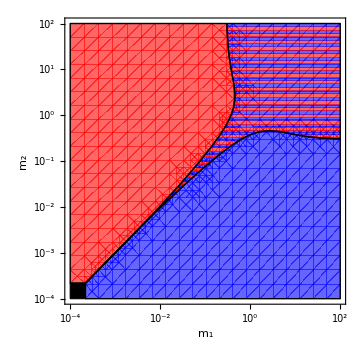

```mathematica
Show[n1wins,n2wins,fc,Graphics[{Black,EdgeForm[Thick],Rectangle[{-4,-4},{-3.66,-3.66}]}],FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},BoundaryStyle->Directive[Black,Thick],ImageSize->Medium,PlotRange->{{-4,2},{-4,2}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-4,2}],None},{Table[{x,Superscript["10",x]},{x,-4,2}],None}}]
```

#### e) α12=α21=1.1

```mathematica
α12=α21=1.1;
```

```mathematica
ClearCache[λ12,λ21];
Clear[m1,m2]
```

```mathematica
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-3.6614287292541534,2},{m2p,-4,2},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-3.6614287292541534,2},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
fc=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]<1,{m1p,-3.6614287292541534,2},{m2p,-3.6614287292541534,2},Mesh->{Table[x,{x,-4,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
```

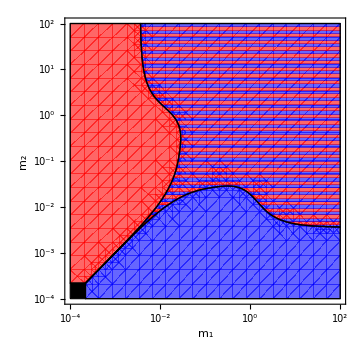

```mathematica
Show[n1wins,n2wins,fc,Graphics[{Black,EdgeForm[Thick],Rectangle[{-4,-4},{-3.66,-3.66}]}],FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},BoundaryStyle->Directive[Black,Thick],ImageSize->Medium,PlotRange->{{-4,2},{-4,2}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-4,2}],None},{Table[{x,Superscript["10",x]},{x,-4,2}],None}}]
```

#### f) α12=α21=1.5

```mathematica
α12=α21=1.5;
```

```mathematica
ClearCache[λ12,λ21];
Clear[m1,m2]
```

```mathematica
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-3.6614287292541534,2},{m2p,-4,2},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-3.6614287292541534,2},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
fc=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]<1,{m1p,-3.6614287292541534,2},{m2p,-3.6614287292541534,2},Mesh->{Table[x,{x,-4,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
```

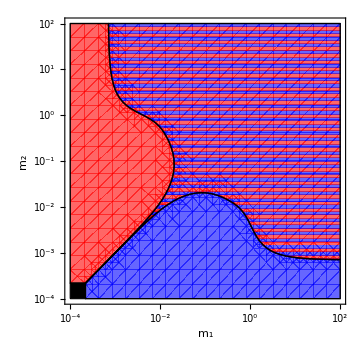

```mathematica
Show[n1wins,n2wins,fc,Graphics[{Black,EdgeForm[Thick],Rectangle[{-4,-4},{-3.66,-3.66}]}],FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},BoundaryStyle->Directive[Black,Thick],ImageSize->Medium,PlotRange->{{-4,2},{-4,2}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-4,2}],None},{Table[{x,Superscript["10",x]},{x,-4,2}],None}}]
```

### Fig 12 — invasion dynamics w/ FORTRAN

Be sure to successfully compile mc21lsodes first. See fortran/README.txt for more information.

#### a) α=1.1, m1=0.01, m2=0.002

```mathematica
mf=25; (* method *)
ml:=n1max+1; (* # lower bands *)
mu:=n1max+1; (* # upper bands *)
rtol=0;
atol=10^-7;

n1max=100;
n2max=100;

Setnmax[n1max,n2max];

r1=1.0;
k1=50;
α12=1.1;
m1=0.01;

r2=1.0;
k2=50;
α21=1.1;
m2=0.002;

e=0.0;
i1=i2=0.0;
```

```mathematica
Clear[nr1,nr2]
```

```mathematica
(* monoculture equilibria and invasion rates *)
{Eq1,Eq2}
{Inv1[nr2/.Eq2],Inv2[nr1/.Eq1]}
```

{{nr1→48.9789},{nr2→48.9787}}

{2.96924,0.158214}

```mathematica
(* make initial conditions for FORTRAN *)
ϵ=50*10^-3;
invdis1=GetDis[{ϵ,nr2/.Eq2}];
dat=ArrayReshape[invdis1/ϵ,{n2max+1,n1max+1}];
ListPlot3D[dat[[All,2;;]],DataRange->{{0,n1max},{0,n2max}},ViewPoint->{-1.8,-2.2,1},AxesEdge->{{-1,-1},{-1,-1},{-1,1}},PlotRange->All,PlotStyle->{Opacity[0.2],Gray},
MeshFunctions->{Sqrt[#3]&},Mesh->50,ImageSize->Large,TicksStyle->frametickstyle]
pinit[n1_,n2_]:=Chop[ArrayReshape[invdis1,{n2max+1,n1max+1}][[n2+1,n1+1]]];
```

-Graphics3D-

```mathematica
(* run FORTRAN simulation *)
tmax=4000.0;
tskip=2.0;
RunSimLSODES
```

time=24.4129 s

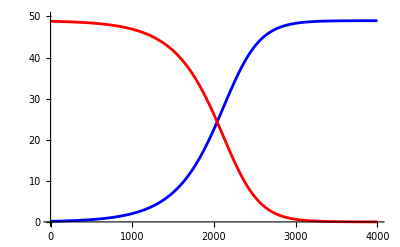

```mathematica
(* Fig. 12a top – n̄ vs t *)
nvst=ListLinePlot[{Table[{t*tskip,GetNr[p[t]]⟦1⟧},{t,0,tend}],Table[{t*tskip,GetNr[p[t]]⟦2⟧},{t,0,tend}]},PlotStyle->{Blue,Red},PlotRange->{0,50},PlotRangePadding->Scaled[.02],TicksStyle->frametickstyle]
```

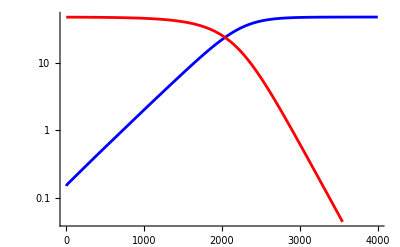

```mathematica
(* Fig. 12a bottom - n̄ vs t - log scale *)
nvst=ListLogPlot[{Table[{t*tskip,GetNr[p[t]]⟦1⟧},{t,0,tend}],Table[{t*tskip,GetNr[p[t]]⟦2⟧},{t,0,tend}]},PlotStyle->{Blue,Red},PlotRange->{0.001*50,50},PlotRangePadding->Scaled[.02],TicksStyle->frametickstyle,Joined->True]
```

#### b) α=1.1, m1=0.1, m2=0.002

```mathematica
mf=25; (* method *)
ml:=n1max+1; (* # lower bands *)
mu:=n1max+1; (* # upper bands *)
rtol=0;
atol=10^-7;

n1max=100;
n2max=100;

Setnmax[n1max,n2max];

r1=1.0;
k1=50;
α12=1.1;
m1=0.1;

r2=1.0;
k2=50;
α21=1.1;
m2=0.002;

e=0.0;
i1=i2=0.0;
```

```mathematica
Clear[nr1,nr2]
```

```mathematica
(* monoculture equilibria and invasion rates *)
{Eq1,Eq2}
{Inv1[nr2/.Eq2],Inv2[nr1/.Eq1]}
```

{{nr1→48.9808},{nr2→48.9787}}

{1.13242,0.0288766}

```mathematica
(* make initial conditions for FORTRAN *)
ϵ=50*10^-3;
invdis1=GetDis[{ϵ,nr2/.Eq2}];
dat=ArrayReshape[invdis1/ϵ,{n2max+1,n1max+1}];
ListPlot3D[dat[[All,2;;]],DataRange->{{0,n1max},{0,n2max}},ViewPoint->{-1.8,-2.2,1},AxesEdge->{{-1,-1},{-1,-1},{-1,1}},PlotRange->All,PlotStyle->{Opacity[0.2],Gray},
MeshFunctions->{Sqrt[#3]&},Mesh->50,ImageSize->Large,TicksStyle->frametickstyle]
pinit[n1_,n2_]:=Chop[ArrayReshape[invdis1,{n2max+1,n1max+1}][[n2+1,n1+1]]];
```

-Graphics3D-

```mathematica
(* run FORTRAN simulation *)
tmax=2000.0;
tskip=2.0;
RunSimLSODES
```

time=27.0847 s

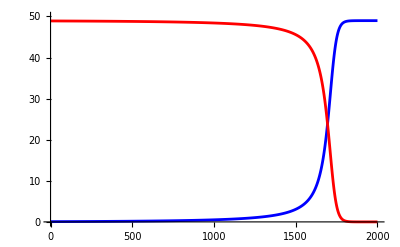

```mathematica
(* Fig. 12b top – n̄ vs t *)
nvst=ListLinePlot[{Table[{t*tskip,GetNr[p[t]]⟦1⟧},{t,0,tend}],Table[{t*tskip,GetNr[p[t]]⟦2⟧},{t,0,tend}]},PlotStyle->{Blue,Red},PlotRange->{0,50},PlotRangePadding->Scaled[.02],TicksStyle->frametickstyle]
```

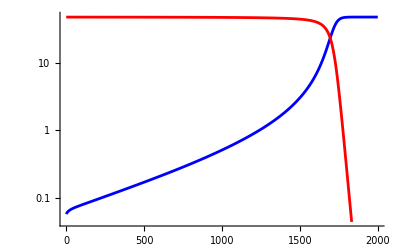

```mathematica
(* Fig. 12b bottom - n̄ vs t - log scale *)
nvst=ListLogPlot[{Table[{t*tskip,GetNr[p[t]]⟦1⟧},{t,0,tend}],Table[{t*tskip,GetNr[p[t]]⟦2⟧},{t,0,tend}]},PlotStyle->{Blue,Red},PlotRange->{0.001*50,50},PlotRangePadding->Scaled[.02],TicksStyle->frametickstyle,Joined->True]
```

### Fig 13 — m1-m2, competition-colonization trade-off

```mathematica
Clear[e]
```

```mathematica
r1=r2=1;
k1=k2=50;
α12=0.5;α21=2.0;
Setnmax[2k1,2k2]
e=0.01;
```

#### a) Outcomes

```mathematica
(* invasion rates *)
λ12[m1in_?NumericQ,m2in_?NumericQ]:=λ12[m1in,m2in]=({m1,m2}={m1in,m2in};Inv1[nr2/.Eq2]);
λ21[m1in_?NumericQ,m2in_?NumericQ]:=λ21[m1in,m2in]=({m1,m2}={m1in,m2in};Inv2[nr1/.Eq1]);
```

```mathematica
ClearCache[λ12,λ21]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

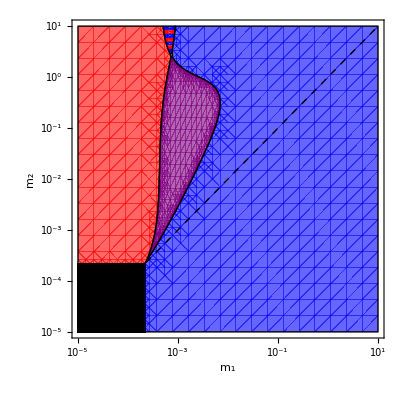

```mathematica
dx=3/41; (* grid spacing for stripes *)

blank=RegionPlot[1<0,{m1p,-5,1},{m2p,-5,1}];
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-5,1},{m2p,-5,1},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-5,1},{m2p,-5,1},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
coex=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,-2},{m2p,-3.8,0.6},MaxRecursion->4,PlotStyle->Directive[Purple,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
fc=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]<1,{m1p,-4,-2},{m2p,0,1},Mesh->{Table[x,{x,-5,1,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
Show[blank,Graphics[{Black,Rectangle[{-5.02,-5.02},{-3.65,-3.65}]}],n1wins,n2wins,coex,fc,Graphics[{Thick,Dashed,Line[{{-5,-5},{1,1}}]}],FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},ImageSize->400,BoundaryStyle->Directive[Black,Thick],PlotRange->{{-5,1},{-5,1}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-5,1}],None},{Table[{x,Superscript["10",x]},{x,-5,1}],None}}]
```

#### b-c) m1=10^-3,m2=10^-2

```mathematica
{m1,m2}={0.001,0.01};
eq=Eq12
```

{nr1→29.3598,nr2→14.8057}

```mathematica
(* Fig. 13b *)
WatershedPlot[GetDis[{nr1,nr2}/.eq],PlotRange->{{0,80},{0,80},{0,0.03}},ImageSize->400]
```

-Graphics3D-

```mathematica
SquarePie[GetDis[{nr1,nr2}/.eq]]
```

-Graphics-

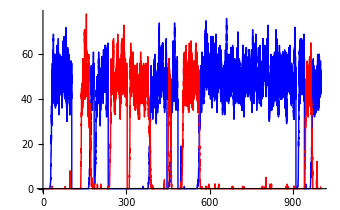

```mathematica
(* Fig. 13c *)
SeedRandom[3];
sol=StochSim[eq,{n1->0,n2->0},1000];
PlotDynamics[sol,PlotPoints->400,PlotRange->Automatic,AxesLabel->None,ImageSize->340,TicksStyle->frametickstyle,LineStyles->Thickness[0.003]]
```

#### d-e) m1=10^-3,m2=10^0

```mathematica
{m1,m2}={0.001,1};
eq=Eq12
```

{nr1→30.5829,nr2→10.9545}

```mathematica
(* Fig 13d *)
WatershedPlot[GetDis[{nr1,nr2}/.eq],PlotRange->{{0,80},{0,80},{0,0.02}},ImageSize->400]
```

-Graphics3D-

```mathematica
SquarePie[GetDis[{nr1,nr2}/.eq]]
```

-Graphics-

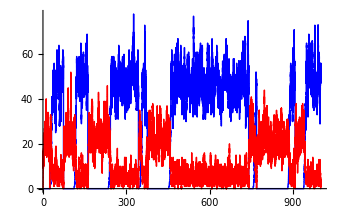

```mathematica
(* Fig 13e *)
SeedRandom[3];
sol=StochSim[eq,{n1->0,n2->0},1000];
PlotDynamics[sol,PlotPoints->400,PlotRange->Automatic,AxesLabel->None,ImageSize->340,TicksStyle->frametickstyle,LineStyles->Thickness[0.003]]
```

### Fig 14 — successional niche trade-off

```mathematica
Clear[e,r1,r2]
```

```mathematica
m1=m2=10^-3;
k1=k2=50;
α12=0.5;α21=2.0;
Setnmax[2k1,2k2]
e=0.01;
```

#### a) Outcomes

```mathematica
ClearCache[λ10,λ20]
```

```mathematica
(* invasion rates into empty environment *)
λ10[r1in_?NumericQ]:=Block[{r1=r1in},NrInOut1[ϵ]/ϵ];
λ20[r2in_?NumericQ]:=Block[{r2=r2in},NrInOut2[ϵ]/ϵ];
```

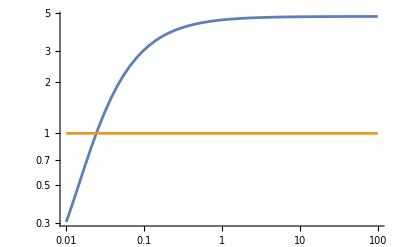

```mathematica
LogLogPlot[{λ10[r1],1},{r1,10^-2,10^2},PlotRange->All]
```

```mathematica
FindRoot[λ10[10^r1p]==1,{r1p,-1.5}]
```

{r1p→-1.61392}

```mathematica
(* minimum r=10^rpmin for species 1 *)
rpmin=-1.615224573191701;
```

```mathematica
LogLogPlot[{λ20[r2],1},{r2,10^-2,10^2},PlotRange->All]
```

-Graphics-

```mathematica
(* minimum r=10^rpmin for species 2 – evidently same as species 1 *)
FindRoot[λ20[10^r2p]==1,{r2p,-1.5}]
```

{r2p→-1.61392}

```mathematica
(* invasion rates *)
λ12[r1in_?NumericQ,r2in_?NumericQ]:=λ12[r1in,r2in]=Block[{r1=r1in,r2=r2in},Inv1[nr2/.Eq2]];
λ21[r1in_?NumericQ,r2in_?NumericQ]:=λ21[r1in,r2in]=Block[{r1=r1in,r2=r2in},Inv2[nr1/.Eq1]];
```

```mathematica
ClearCache[λ12,λ21]
```

```mathematica
blank=RegionPlot[1<0,{r1p,-2,1},{r2p,-2,1}];
```

```mathematica
(* 250 s *)
n1wins=RegionPlot[λ12[10^r1p,10^r2p]>1&&λ21[10^r1p,10^r2p]<1,{r1p,rpmin,1},{r2p,-2,1},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 200 s *)
n2wins=RegionPlot[λ12[10^r1p,10^r2p]<1&&λ21[10^r1p,10^r2p]>1,{r1p,-2,1},{r2p,rpmin,1},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 845 s *)
coex=RegionPlot[λ12[10^r1p,10^r2p]>1&&λ21[10^r1p,10^r2p]>1,{r1p,rpmin,1},{r2p,rpmin,1},MaxRecursion->4,PlotStyle->Directive[Purple,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

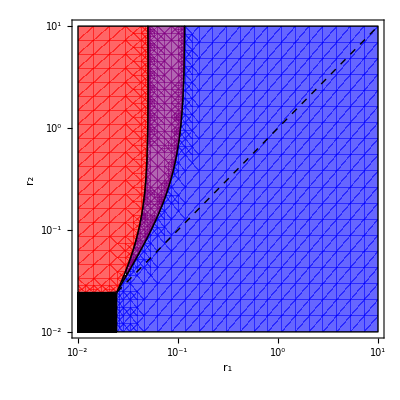

```mathematica
Show[blank,Graphics[{Black,Rectangle[{-2.01,-2.01},{rpmin,rpmin}]}],n1wins,coex,n2wins,Graphics[{Thick,Dashed,Line[{{-2,-2},{1,1}}]}],FrameStyle->Directive[18,Black],FrameLabel->{Style["r_1",21],Style["r_2",21]},ImageSize->400,BoundaryStyle->Directive[Black,Thick],PlotRange->{{-2,1},{-2,1}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-2,1}],None},{Table[{x,Superscript["10",x]},{x,-2,1}],None}}]
```

#### b-c) r1=0.1,r2=10

```mathematica
{r1,r2}={0.1,10.};
eq=Eq12
```

{nr1→19.6288,nr2→7.2145}

```mathematica
WatershedPlot[GetDis[{nr1,nr2}/.eq],PlotRange->{{0,80},{0,80},{0,0.025}},ImageSize->400]
```

-Graphics3D-

```mathematica
SquarePie[GetDis[{nr1,nr2}/.eq]]
```

-Graphics-

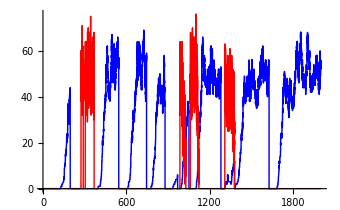

```mathematica
(* Fig. 13c *)
SeedRandom[3];
sol=StochSim[eq,{n1->0,n2->0},2000];
PlotDynamics[sol,PlotPoints->400,PlotRange->Automatic,AxesLabel->None,ImageSize->340,TicksStyle->frametickstyle,LineStyles->Thickness[0.003]]
```